#### Case 1: Trophic transmission; one specialist parasite; parasite regulates definitive host population size; parasite avoids already infected hosts

Let D_1 and D_2 be two definitive hosts and N be prey of both and the intermediate host. One touchy bit is how to deal with the effect of ingestion on both the dynamics of predator (the definitive host) and prey (the intermediate host). One possibility is that infection is embedded within a classic predator-prey model, where both predator and prey growth are impacted by one another. Such a model is quite different from the direct life cycle model studied in the main text, and is also very difficult to analyze. A second possibility is that prey density is constant; in this model you cannot assume that predator growth is entirely determined by prey ingestion (as in a classic predator-prey model) because the predator population will either grow or decay exponentially. We consider two possibilities: that the predator population is growing logistically or that it is constant. 

Here we assume that the intermediate host (the prey) has a constant population size. We let N_T be the total population size, and N_(I,r) and N_(I,m) be the abundance of intermedate host infected with the resident (specialist) and mutant (generalist) parasites, respectively. We don’t need to track the number of susceptible intermediate hosts. The two definitive hosts both grow logistically in the absence of infection, with no direct effect of prey ingestion on their growth rate. One way to justify this assumption is to assume that the predators are eating lots of different prey items, so that their dynamics are largely independent of this particular prey item. However, infection is assumed to have an effect on the growth of the definitive host. We let D_(1,S) and D_(2,S) to be the number of primary and secondary definitive hosts that are susceptible to infection; D_(1,I,r) is the number of primary definitive hosts infected by the specialist (resident) parasite; we assume that the secondary definitive host is not infected by its own specialist parasite. D_(1,I,m) and D_(2,I,m) are the numbers of primary and secondary definitive hosts infected by the generalist (mutant) parasite. Definitive hosts shed parasite back into the environment, with P_r and P_m the abundance of specialist and generalist in the environment. These parasites are consumed by the intermediate host, which can then transmit the parasite to the definitive host upon ingestion.

The full system is given below.

```mathematica
dNirdt=β (NT-Nir-Nim) Pr-a1 (D1s+D1ir+D1im)Nir-a2(D2s+D2im) Nir;
dNimdt=β (NT-Nir-Nim) Pm-a1 (D1s+D1ir+D1im)Nim-a2 (D2s+D2im) Nim;
dD1sdt=r1 (D1s+D1ir+D1im) (1-(D1s+D1ir+D1im)/K1)-a1 D1s (Nir+Nim);
dD2sdt=r2 (D2s+D2im) (1-(D2s+D2im)/K2)-a2 D2s Nim;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;
dPrdt=λ1 D1ir-β (NT-Nir-Nim) Pr-γ Pr;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-Nir-Nim) Pm-γ Pm;
```

The Jacobian matrix for this system is quite large, but has the same block triangular structure that we have observed previously.

```mathematica
J={{D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 Nir+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
-a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s-Pr β | -a1 Nir | (-Nir+NT) β | -Pr β | -a1 Nir | -a2 Nir | 0
a1 Nir | 0 | a1 D1s | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | Pr β | λ1 | -(-Nir+NT) β-γ | Pr β | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
0 | 0 | 0 | 0 | 0 | a1 D1s | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | a2 D2s | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

Because J is upper triangular, the eigenvalues are given by the eigenvalues of the submatrices that fall on the diagonal of J. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below.

```mathematica
MatrixForm[J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s | 0 | 0 | (-Nir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-Nir+NT) β-γ)

We can apply the next generation matrix theorem to determine the stability.

```mathematica
F={{0,0,0, β (NT-Nir)},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s)+a2 D2s,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β (NT-Nir)+γ}};
(J[[6;;9,6;;9]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) (Nir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Nir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue, which can be rewritten as R_0=(β N_s N_T)/(β N_s N_T+γ)((a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_1)/μ_1+(a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S))(c λ_2)/μ_2), which has a nice intuitive meaning: (β (N_T-N_(I r)))/(β (N_T-N_(I r))+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; (a_1 D_(1,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a susceptible primary definitive host; (a_2 D_(2,S))/(a_1 D_(1,S)+a_1 D_(1,I,r)+a_2 D_(2,S)) is the probability that an infected intermediate host is ingested by a suceptible secondary definitive host; (c λ_1)/μ_1 and (c λ_2)/μ_2 are the expected number of parasites shed from infected primary and secondary definitive hosts, respectively.

```mathematica
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)//Simplify
```

True

To determine how changing parameters affects R_0 for this model, we need to know the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) when the generalist parasite is not present. We know that D_(2,S)=K_2, the carrying capacity for the secondary host, but the other values are more difficult to determine.

```mathematica
PrEq=Simplify[Solve[(dNirdt/.{Nim->0,D1im->0,D2im->0})==0,Pr]][[1]]
```

{Pr→-((a1 (D1ir+D1s)+a2 D2s) Nir)/((Nir-NT) β)}

```mathematica
NirEq=Simplify[Solve[(dD1sdt/.{Nim->0,D1im->0})==0,Nir]][[1]]
```

{Nir→-((D1ir+D1s) (D1ir+D1s-K1) r1)/(a1 D1s K1)}

```mathematica
D1sEq=Assuming[K1>0,Simplify[Solve[(dD1irdt/.NirEq)==0,D1s][[2]]]]
```

{D1s→(-2 D1ir r1+K1 r1+√(K1 r1 (K1 r1-4 D1ir μ1)))/(2 r1)}

```mathematica
D1irEq=Solve[Numerator[Simplify[dPrdt/.PrEq/.NirEq/.D1sEq]]==0,D1ir]
```

{{D1ir→0},{D1ir→1},1,{D1ir→-(47+a1^2 K1 r1 β^2 μ1^5)/(3 (a1^4 NT^2 r1^2 β^2 λ1^2+2 a1^3 NT r1^2 β^2 λ1^2 μ1+a1^2 r1^2 β^2 λ1^2 μ1^2))+1/1-((1+ⅈ √3) 1^1)/(6 2^1 (1))}}
 |  |  |  |

Because of the complexity of these expressions for the equilibria, we cannot explore the question of how changing parameters affects R_0 analytically. Instead, we will use numerical exploration to see whether changing mass/temperature have any effect on invasion fitness. As before, we use simple allometric scaling relationships to relate key processes to host body size and temperature. Additionally, we assume that the growth rate of the definitive host (r) depends on body size as well.
r=r_0 e^(E/k T)W^-0.25
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites).

Values for .08.08E, k, r_0,K_0, and μ_0 that are appropriate for fish come from Savage et al. 2004. The estimate of λ_0 is modified from Poulin & George-Nascimento 2007. 

The function below uses numerical simulation to determine the equilibrium values of N_s, D_(1,S), D_(1,I,r), and D_(2,S) for the specified parameters. These values are then plugged into the R_0 expression to calculate the invasion fitness.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
Nir'[t]==β (NT-Nir[t]) Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t],
D1ir'[t]==a1 D1s[t] Nir[t]-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β (NT-Nir[t]) Pr[t]-γ Pr[t],
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{Ns->(Ns[1000]/.Soln)[[1]],Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],Pr->(Pr[1000]/.Soln)[[1]]}];*)
(β (NT-Nir))/(β (NT-Nir)+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

For these parameters, increasing body mass increases R_0:

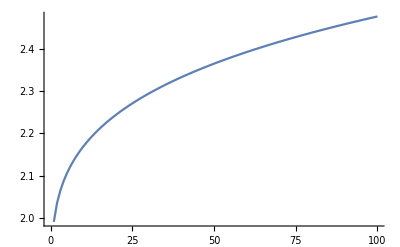

```mathematica
InvFitAcrossW=Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,0.1],{W,10,1000,10}];
ListLinePlot[InvFitAcrossW]
```

This is true if you increase the temperature (here increasing temperature from 270 to 310). Notice, however, that R_0 is lower for higher temperatures, indicating that increasing temperature negatively affects R_0.

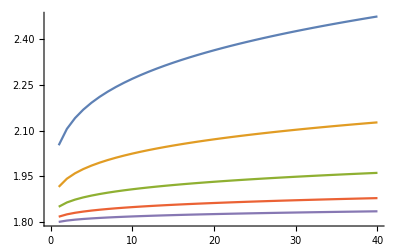

```mathematica
InvFitAcrossWT=Table[Table[NumSolInvFit[W,T,0.9,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{T,270,310,10}];
ListLinePlot[InvFitAcrossWT]
```

It also holds if you increase the cost of generalism (here decreasing c from 0.9 to 0.5):

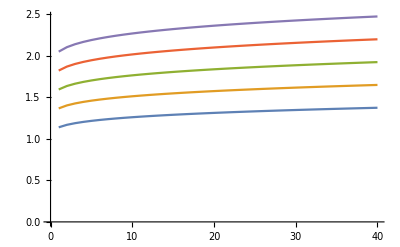

```mathematica
InvFitAcrossWc=Table[Table[NumSolInvFit[W,270,c,0.9,1,0.1,0.01,0.1],{W,25,1000,25}],{c,0.5,0.9,0.1}];ListLinePlot[InvFitAcrossWc]
```

It also holds if you reduce the size of the secondary host (here decreasing f from 0.9 to 0.5):

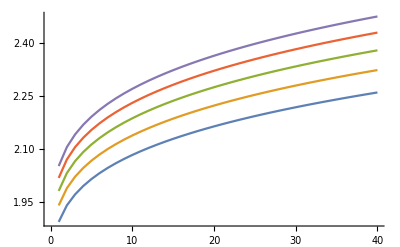

```mathematica
InvFitAcrossWf=Table[Table[NumSolInvFit[W,270,0.9,f,1,0.1,0.01,0.1],{W,25,1000,25}],{f,0.5,0.9,0.1}];
ListLinePlot[InvFitAcrossWf]
```

It also holds if you reduce the number of intermediate hosts (here N_T ranges from 0.25 to 2):

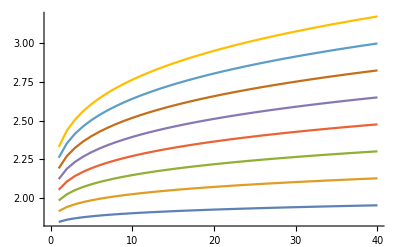

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.1,0.01,0.1],{W,25,1000,25}],{NT,0.25,2,0.25}];
ListLinePlot[InvFitAcrossWNT]
```

It also holds if you change the transmission rate to intermediate hosts (here β ranges from 0.05 to 0.55):

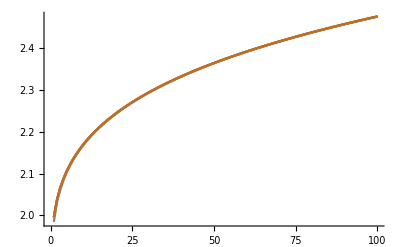

```mathematica
InvFitAcrossWB=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,B,0.01,0.1],{W,10,1000,10}],{B,0.05,0.55,0.1}];
ListLinePlot[InvFitAcrossWB]
```

It also holds if you change the rate parasites are lost from the environment (here γ ranges from 0.01 to 0.1):

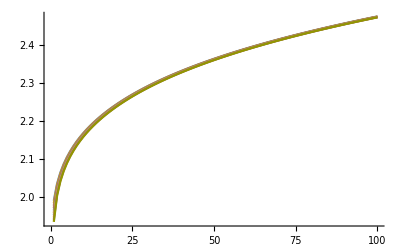

```mathematica
InvFitAcrossWg=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,g,0.1],{W,10,1000,10}],{g,0.01,0.1,0.01}];
ListLinePlot[InvFitAcrossWg]
```

It also holds if you change the ingestion rate of the definitive hosts:

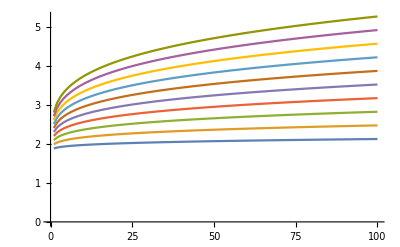

```mathematica
InvFitAcrossWa=Table[Table[NumSolInvFit[W,270,0.9,0.9,1,0.1,0.01,a],{W,10,1000,10}],{a,0.05,0.5,0.05}];
ListLinePlot[InvFitAcrossWa]
```

Increasing temperature decreases R_0:

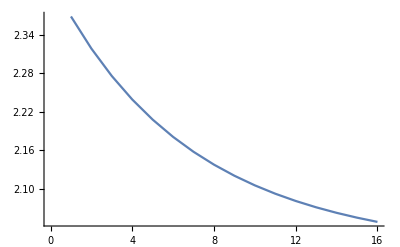

```mathematica
InvFitAcrossT=Table[NumSolInvFit[100,T,0.9,0.9,1],{T,270,300,2}];
ListLinePlot[InvFitAcrossT]
```

#### Case 1: Trophic transmission; one specialist parasite; parasite regulates definitive host population size; parasite avoids already infected hosts

Now we assume that there are two specialist parasites exploiting the same intermediate host, but infecting

```mathematica
dN1irdt=β (NT-N1ir-N2ir-Nim) P1r-a1(D1s+D1ir+D1im) N1ir-a2(D2s+D2ir+D2im) N1ir;
dN2irdt=β (NT-N1ir-N2ir-Nim) P2r-a1(D1s+D1ir+D1im)N2ir-a2 (D2s+D2ir+D2im) N2ir;
dNimdt=β (NT-N1ir-N2ir-Nim) Pm-a1(D1s+D1ir+D1im) Nim-a2 (D2s+D2ir+D2im) Nim;

dD1sdt=r1 (D1s+D1ir+D1im)(1-(D1s+D1ir+D1im)/K1)-a1 D1s (N1ir+Nim);
dD2sdt=r2 (D2s+D2ir+D2im)(1-(D2s+D2ir+D2im)/K2)-a2 D2s (N2ir+Nim);
dD1irdt=a1 D1s N1ir-μ1 D1ir;
dD2irdt=a2 D2s N2ir-μ2 D2ir;
dD1imdt=a1 D1s Nim-μ1 D1im;
dD2imdt=a2 D2s Nim-μ2 D2im;

dP1rdt=λ1 D1ir-β (NT-N1ir-N2ir-Nim) P1r-γ P1r;
dP2rdt=λ2 D2ir-β (NT-N1ir-N2ir-Nim) P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β (NT-N1ir-N2ir-Nim) Pm-γ Pm;
```

To determine whether the generalist can invade this system, we again look at the Jacobian.

```mathematica
J={{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r],
D[dN1irdt,N2ir],D[dN1irdt,D2s],D[dN1irdt,D2ir],D[dN1irdt,P2r],
D[dN1irdt,Nim],D[dN1irdt,D1im],D[dN1irdt,D2im],D[dN1irdt,Pm]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r],
D[dD1sdt,N2ir],D[dD1sdt,D2s],D[dD1sdt,D2ir],D[dD1sdt,P2r],
D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r],
D[dD1irdt,N2ir],D[dD1irdt,D2s],D[dD1irdt,D2ir],D[dD1irdt,P2r],
D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r],
D[dP1rdt,N2ir],D[dP1rdt,D2s],D[dP1rdt,D2ir],D[dP1rdt,P2r],
D[dP1rdt,Nim],D[dP1rdt,D1im],D[dP1rdt,D2im],D[dP1rdt,Pm]},
{D[dN2irdt,N1ir],D[dN2irdt,D1s],D[dN2irdt,D1ir],D[dN2irdt,P1r],
D[dN2irdt,N2ir],D[dN2irdt,D2s],D[dN2irdt,D2ir],D[dN2irdt,P2r],
D[dN2irdt,Nim],D[dN2irdt,D1im],D[dN2irdt,D2im],D[dN2irdt,Pm]},
{D[dD2sdt,N1ir],D[dD2sdt,D1s],D[dD2sdt,D1ir],D[dD2sdt,P1r],
D[dD2sdt,N2ir],D[dD2sdt,D2s],D[dD2sdt,D2ir],D[dD2sdt,P2r],
D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dD2irdt,N1ir],D[dD2irdt,D1s],D[dD2irdt,D1ir],D[dD2irdt,P1r],
D[dD2irdt,N2ir],D[dD2irdt,D2s],D[dD2irdt,D2ir],D[dD2irdt,P2r],
D[dD2irdt,Nim],D[dD2irdt,D1im],D[dD2irdt,D2im],D[dD2irdt,Pm]},
{D[dP2rdt,N1ir],D[dP2rdt,D1s],D[dP2rdt,D1ir],D[dP2rdt,P1r],
D[dP2rdt,N2ir],D[dP2rdt,D2s],D[dP2rdt,D2ir],D[dP2rdt,P2r],
D[dP2rdt,Nim],D[dP2rdt,D1im],D[dP2rdt,D2im],D[dP2rdt,Pm]},
{D[dNimdt,N1ir],D[dNimdt,D1s],D[dNimdt,D1ir],D[dNimdt,P1r],
D[dNimdt,N2ir],D[dNimdt,D2s],D[dNimdt,D2ir],D[dNimdt,P2r],
D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,N1ir],D[dD1imdt,D1s],D[dD1imdt,D1ir],D[dD1imdt,P1r],
D[dD1imdt,N2ir],D[dD1imdt,D2s],D[dD1imdt,D2ir],D[dD1imdt,P2r],
D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,N1ir],D[dD2imdt,D1s],D[dD2imdt,D1ir],D[dD2imdt,P1r],
D[dD2imdt,N2ir],D[dD2imdt,D2s],D[dD2imdt,D2ir],D[dD2imdt,P2r],
D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,N1ir],D[dPmdt,D1s],D[dPmdt,D1ir],D[dPmdt,P1r],
D[dPmdt,N2ir],D[dPmdt,D2s],D[dPmdt,D2ir],D[dPmdt,P2r],
D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}}/.{Nim->0,D1im->0,D2im->0,Pm->0};
```

As before, this matrix is upper block triangular. The upper left submatrix determines the stability of the system that doesn’t include the generalist parasite. It will be helpful to look at the eigenvalues of this submatrix at the parasite-free equilibrium when both specialist parasites are absent (N_(1I r)=0, N_(2I r)=0, D_(1S)=K_1, D_(1 I r)=0, D_(2 S)=K_2, D_(2 I r)=0, P_1=0, P_2=0)? In particular, we want all of these eigenvalues to be positive to guarantee that the specialist parasites can both persist in the system. Notice that this matrix is block diagonal, so we can simply look at the eigenvalues of each submatrix to determine the eigenvalues of the full matrix.

```mathematica
J[[1;;8,1;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0}//MatrixForm
```

(-a1 K1-a2 K2 | 0 | 0 | NT β | 0 | 0 | 0 | 0
-a1 K1 | -r1 | -r1 | 0 | 0 | 0 | 0 | 0
a1 K1 | 0 | -μ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | λ1 | -NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a1 K1-a2 K2 | 0 | 0 | NT β
0 | 0 | 0 | 0 | -a2 K2 | -r2 | -r2 | 0
0 | 0 | 0 | 0 | a2 K2 | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | λ2 | -NT β-γ)

Applying the next generation matrix, we find that for the specialist-absent system to be unstable, we require that
(β N_T)/(β N_T+γ) ((a_1 K_1)/(a_1 K_1+a_2 K_2)λ_1/μ_1)>1 and (β N_T)/(β N_T+γ) ((a_2 K_2)/(a_1 K_1+a_2 K_2)λ_2/μ_2)>1

```mathematica
F1={{0,0,0,NT β},{0,0,0,0},{a1 K1,0,0,0},{0,0,λ1,0}};
V1={{a1 K1+a2 K2,0,0,0},{a1 K1,r1,r1,0},{0,0,μ1,0},{0,0,0,NT β+γ}};
(J[[1;;4,1;;4]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F1-V1
Eigenvalues[Dot[F1,Inverse[V1]]]
(Eigenvalues[Dot[F1,Inverse[V1]]][[2]])^3==(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)
F2={{0,0,0,NT β},{0,0,0,0},{a2 K2,0,0,0},{0,0,λ2,0}};
V2={{a1 K1+a2 K2,0,0,0},{a2 K2,r2,r2,0},{0,0,μ2,0},{0,0,0,NT β+γ}};
(J[[5;;8,5;;8]]/.{N1ir->0,N2ir->0,D1s->K1,D1ir->0,D2s->K2,D2ir->0,P1r->0,P2r->0})==F2-V2
Eigenvalues[Dot[F2,Inverse[V2]]]
(Eigenvalues[Dot[F2,Inverse[V2]]][[2]])^3==(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)
```

True

{0,(a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) a1^(1/3) K1^(1/3) NT^(1/3) β^(1/3) λ1^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ1^(1/3))}

True

True

{0,(a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) a2^(1/3) K2^(1/3) NT^(1/3) β^(1/3) λ2^(1/3))/((a1 K1+a2 K2)^(1/3) (NT β+γ)^(1/3) μ2^(1/3))}

True

We assume that both of those inequalities are satisfied. Whether the generalist can invade the system depends on the eigenvalues of the lower right submatrix of J:

```mathematica
MatrixForm[J[[9;;12,9;;12]]]
```

(-a1 (D1ir+D1s)-a2 (D2ir+D2s) | 0 | 0 | (-N1ir-N2ir+NT) β
a1 D1s | -μ1 | 0 | 0
a2 D2s | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -(-N1ir-N2ir+NT) β-γ)

Using the next generation matrix theorem, the Jacobian will have a positive eigenvalue whenever the second value is greater than 1.

```mathematica
F={{0,0,0,(NT-N1ir-N2ir) β},{a1 D1s,0,0,0},{a2 D2s,0,0,0},{0,c λ1,c λ2,0}};
V={{a1 (D1ir+D1s)+a2(D2ir+D2s),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,(NT-N1ir-N2ir) β+γ}};
J[[9;;12,9;;12]]==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{0,(c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3))}

This eigenvalue is equivalent to the expression given below:

```mathematica
((c^(1/3) (N1ir+N2ir-NT)^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2ir+a2 D2s)^(1/3) (N1ir β+N2ir β-NT β-γ)^(1/3) μ1^(1/3) μ2^(1/3)))^3==((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) ((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)//Simplify
```

True

As before, it is impossible to make headway analytically, so we must resort to numerical solutions.

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot,B,g,a},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->B,γ->g,a1->a,a2->a,NT->NTot};
(*Print[(β NT)/(β NT+γ)((a1 K1)/(a1 K1+a2 K2) λ1/μ1)/.allom/.pars];*)
(*Print[(β NT)/(β NT+γ)((a2 K2)/(a1 K1+a2 K2) λ2/μ2)/.allom/.pars];*)
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({
N1ir'[t]==β (NT-N1ir[t]-N2ir[t]) P1r[t]-a1(D1s[t]+D1ir[t]) N1ir[t]-a2(D2s[t]+D2ir[t]) N1ir[t],
N2ir'[t]==β (NT-N1ir[t]-N2ir[t]) P2r[t]-a1(D1s[t]+D1ir[t]) N2ir[t]-a2(D2s[t]+D2ir[t]) N2ir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] N1ir[t],
D2s'[t]==r2 (D2s[t]+D2ir[t]) (1-(D2s[t]+D2ir[t])/K2)-a2 D2s[t] N2ir[t],
D1ir'[t]==a1 D1s[t] N1ir[t]-μ1 D1ir[t],
D2ir'[t]==a2 D2s[t] N2ir[t]-μ1 D2ir[t],
P1r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P1r[t]-γ P1r[t],
P2r'[t]==λ1 D1ir[t]-β (NT-N1ir[t]-N2ir[t]) P2r[t]-γ P2r[t],
N1ir[0]==0,N2ir[0]==0,
D1s[0]==0.1,D2s[0]==0.1,
D1ir[0]==0,D2ir[0]==0,
P1r[0]==1,P2r[0]==1}/.allom/.pars),
{N1ir,N2ir,D1s,D1ir,D2s,D2ir,P1r,P2r},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(* Print[{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}] *);
((NT-N1ir-N2ir) β)/((NT-N1ir-N2ir) β+γ) ((a1 D1s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ1)/μ1+(a2 D2s)/(a1 (D1ir+D1s)+a2 (D2ir+D2s)) (c λ2)/μ2)/.{N1ir->(N1ir[1000]/.Soln)[[1]],N2ir->(N2ir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],D2s->(D2s[1000]/.Soln)[[1]],D2ir->(D2ir[1000]/.Soln)[[1]]}/.allom/.pars
];
```

One case is sufficient to demonstrate that the response of the generalist’s R_0 to changes in host body size is much more complex here. Consider the effect of changing the definitive host body sizes across a gradient of intermediate host abundance. You can see very clearly that the responses depend on the value of N_T: when N_T is small, increasing host mass increases R_0; when N_T is large, increasing host mass first increases, then decreases R_0. 

In reality, the abundance of the definitive host’s prey is likely to be related to the size of the definitive host: in general, larger-bodied hosts are more likely to consume larger-bodied prey, whose carrying capacities would decrease commensurately. That is, as definitive host body size goes up, you would expect intermediate host carrying capacity to go down.

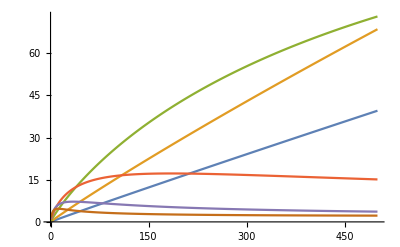

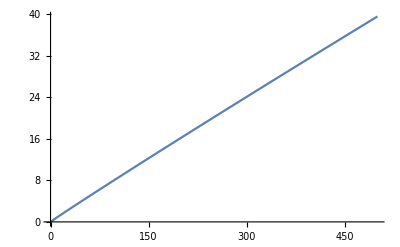

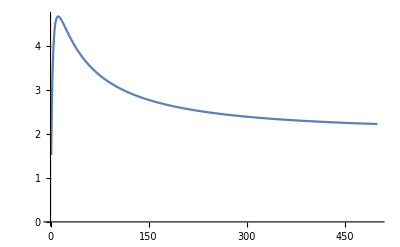

```mathematica
InvFitAcrossWNT=Table[Table[NumSolInvFit[W,270,0.9,0.9,NT,0.01,0.1,0.01],{W,10,5000,10}],{NT,{0.1,0.2,0.5,1,1.5,2}}];
ListLinePlot[InvFitAcrossWNT]
ListLinePlot[InvFitAcrossWNT[[1]]]
ListLinePlot[InvFitAcrossWNT[[6]]]
```

Increasing temperature also has a much more complex effect on R_0: when N_T is large, increasing temperature increases R_0, but when N_T is small, increasing temperature decreases R_0.

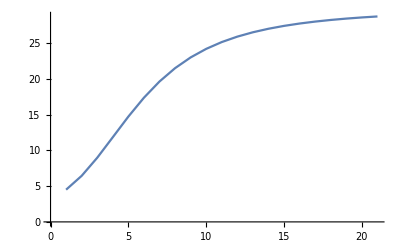

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,2,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

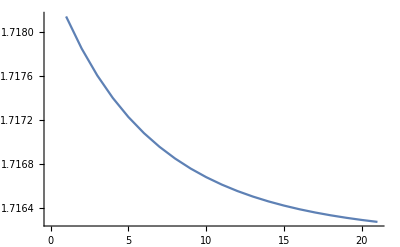

```mathematica
InvFitAcrossWT=Table[NumSolInvFit[200,T,0.9,0.9,0.1,0.01,0.1,0.01],{T,270,310,2}];
ListLinePlot[InvFitAcrossWT]
```

#### asdlkfj

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-c N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-c N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-c N12m (K1+K2);

dI1rdt=c(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=c(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=c(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=c(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r (KN-N1r-N2r-N12m)-γ P1r;
dP2rdt=λ2 I2r-β P2r (KN-N1r-N2r-N12m)-γ P2r;
dP12mdt=a λ1 I1m+a λ2 I2m-β P12m (KN-N1r-N2r-N12m)-γ P12m;
```

The Jacobian is needed to inform us about the stability of the system.

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}};
```

Before we can investigate whether the generalist can invade or not, we need to establish the conditions necessary for the specialist parasites to be able to persist in the system. That is, we are interested in the stability of the equilibrium where N_(1r), N_(2r),I_(1r), I_(2r), P_(1r) and P_(2r) are all equal to 0.

```mathematica
J[[1;;6,1;;6]]/.{N1r->0,N2r->0,I1r->0,I2r->0,P1r->0,P2r->0,N12m->0,I1m->0,I2m->0,P12m->0}//MatrixForm
```

(-c (K1+K2) | 0 | 0 | 0 | KN β | 0
0 | -c (K1+K2) | 0 | 0 | 0 | KN β
c K1 | 0 | -μ1 | 0 | 0 | 0
0 | c K2 | 0 | -μ2 | 0 | 0
0 | 0 | λ1 | 0 | -KN β-γ | 0
0 | 0 | 0 | λ2 | 0 | -KN β-γ)

Applying the next generation matrix theorem:

```mathematica
F={{0,0,0,0,KN β,0},{0,0,0,0,0,KN β},{c K1,0,0,0,0,0},{0,c K2,0,0,0,0},{0,0,λ1,0,0,0},{0,0,0,λ2,0,0}};
V={{c (K1+K2),0,0,0,0,0},{0,c (K1+K2),0,0,0,0},{0,0,μ1,0,0,0},{0,0,0,μ2,0,0},{0,0,0,0,KN β+γ,0},{0,0,0,0,0,KN β+γ}};
(J[[1;;6,1;;6]]/.{N1r->0,N2r->0,I1r->0,I2r->0,P1r->0,P2r->0,N12m->0,I1m->0,I2m->0,P12m->0})==F-V
Eigenvalues[Dot[F,Inverse[V]]]
```

True

{(K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) K2^(1/3) KN^(1/3) β^(1/3) λ2^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ2^(1/3)),(K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) K1^(1/3) KN^(1/3) β^(1/3) λ1^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3))}

This equilibrium will be unstable, allowing both specialists to persist, as long as both (K1 KN β λ1)/((K1+K2) (KN β+γ) μ1) > 0 and (K2 KN β λ2)/((K1+K2) (KN β+γ) μ2)> 0.

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{N12m->0,I1m->0,I2m->0,P12m->0}]
```

(-c (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
c (-I1r+K1) | -μ1 | 0 | 0
c (-I2r+K2) | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -(KN-N1r-N2r) β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{c S1,0,0,0},{c S2,0,0,0},{0,a λ1, a λ2,0}};
V={{c(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β KN+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-c (K1+K2) | 0 | 0 | Ns β
c S1 | -μ1 | 0 | 0
c S2 | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

{0,(a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(a β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 ))/((K_1+K_2)(β K_N+γ) μ_1 μ_2)>1
a λ β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 )>(K_1+K_2)(β K_N+γ) μ_1 μ_2
(β N_s)/(β K_N+γ) (a λ_2 μ_1 S_2+a λ_1 μ_2 S_1)>(K_1+K_2) μ_1 μ_2
(β N_s)/(β K_N+γ) (S_1/(K_1+K_2)(a λ_1)/μ_1 +S_2/(K_1+K_2)(a λ_2)/μ_2 )>1

where
(β N_s)/(β K_N+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(a λ_1)/μ_1 and (a λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β KN+γ) (S1/(K1+K2) (a λ1)/μ1+S2/(K1+K2) (a λ2)/μ2);
```

To find the generalist-free equilibrium, we first make use of the fact that (dP_(1r))/dt=0 implies that β P_(1r)(K_N-N_(1r)-N_(2r))=λ_1 I_(1r)-γ P_(1r) and that (dP_(2r))/dt=0 implies that β P_(2r)(K_N-N_(1r)-N_(2r))=λ_2 I_(2r)-γ P_(2r).

```mathematica
I1rEq=Solve[λ1 I1r-γ P1r-c N1r (K1+K2)==0,I1r][[1,1,2]]
I2rEq=Solve[λ2 I2r-γ P2r-c N2r (K1+K2)==0,I2r][[1,1,2]]
```

(c K1 N1r+c K2 N1r+P1r γ)/λ1

(c K1 N2r+c K2 N2r+P2r γ)/λ2

```mathematica
P1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,P1r][[1,1,2]]
P2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,P2r][[1,1,2]]
```

(-c^2 K1 N1r^2-c^2 K2 N1r^2+c K1 N1r λ1-c K1 N1r μ1-c K2 N1r μ1)/(γ (c N1r+μ1))

(-c^2 K1 N2r^2-c^2 K2 N2r^2+c K2 N2r λ2-c K1 N2r μ2-c K2 N2r μ2)/(γ (c N2r+μ2))

```mathematica
I1rEq/.P1r->P1rEq//Simplify
I2rEq/.P2r->P2rEq//Simplify
```

(c K1 N1r)/(c N1r+μ1)

(c K2 N2r)/(c N2r+μ2)

```mathematica
N1rEq=Solve[(dP1rdt/.I1r->I1rEq/.P1r->P1rEq/.{N12m->0})==0,N1r]
```

{{N1r→0},{N1r→1/(2 (-c K1 β-c K2 β))(-c K1 KN β-c K2 KN β+c K1 N2r β+c K2 N2r β-c K1 γ-c K2 γ-K1 β λ1+K1 β μ1+K2 β μ1-√((c K1 KN β+c K2 KN β-c K1 N2r β-c K2 N2r β+c K1 γ+c K2 γ+K1 β λ1-K1 β μ1-K2 β μ1)^2-4 (-c K1 β-c K2 β) (-K1 KN β λ1+K1 N2r β λ1+K1 KN β μ1+K2 KN β μ1-K1 N2r β μ1-K2 N2r β μ1+K1 γ μ1+K2 γ μ1)))},{N1r→1/(2 (-c K1 β-c K2 β))(-c K1 KN β-c K2 KN β+c K1 N2r β+c K2 N2r β-c K1 γ-c K2 γ-K1 β λ1+K1 β μ1+K2 β μ1+√((c K1 KN β+c K2 KN β-c K1 N2r β-c K2 N2r β+c K1 γ+c K2 γ+K1 β λ1-K1 β μ1-K2 β μ1)^2-4 (-c K1 β-c K2 β) (-K1 KN β λ1+K1 N2r β λ1+K1 KN β μ1+K2 KN β μ1-K1 N2r β μ1-K2 N2r β μ1+K1 γ μ1+K2 γ μ1)))}}

```mathematica
N2rEq=Simplify[Solve[(dP2rdt/.I2r->I2rEq/.P2r->P2rEq/.{N12m->0}/.N1r->N1rEq[[2,1,2]])==0,N2r]]
```

{{N2r→0},{N2r→1/(2 c^2 β (K1 λ1+K2 λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))},{N2r→1/(2 c^2 β (K1 λ1+K2 λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2+√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))}}

```mathematica
KN-(N1rEq[[2,1,2]]/.N2r->N2rEq[[2,1,2]])-N2rEq[[2,1,2]]//Simplify
```

KN-1/(2 c^2 β (K1 λ1+K2 λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))-1/(2 c (K1+K2) β)(c K1 KN β+c K2 KN β+c K1 γ+c K2 γ+K1 β λ1-K1 β μ1-K2 β μ1-1/(2 c (K1 λ1+K2 λ2))K1 (c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))-1/(2 c (K1 λ1+K2 λ2))K2 (c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))+√(1/(4 c^2 (K1 λ1+K2 λ2)^2)(2 c^2 K1^2 KN β λ1+2 c^2 K1 K2 KN β λ1+2 c^2 K1^2 γ λ1+2 c^2 K1 K2 γ λ1+2 c K1^2 β λ1^2+c^2 K1 K2 KN β λ2+c^2 K2^2 KN β λ2+c^2 K1 K2 γ λ2+c^2 K2^2 γ λ2+c K1 K2 β λ1 λ2-c K2^2 β λ2^2-2 c K1^2 β λ1 μ1-2 c K1 K2 β λ1 μ1-3 c K1 K2 β λ2 μ1-3 c K2^2 β λ2 μ1+2 c K1^2 β λ1 μ2+2 c K1 K2 β λ1 μ2+c K1 K2 β λ2 μ2+c K2^2 β λ2 μ2+K1 √(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2))))))+K2 √(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))^2+4 c (K1+K2) β (-K1 KN β λ1+K1 KN β μ1+K2 KN β μ1+K1 γ μ1+K2 γ μ1+1/(2 c^2 (K1 λ1+K2 λ2))K1 λ1 (c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))-1/(2 c^2 (K1 λ1+K2 λ2))K1 μ1 (c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))))-1/(2 c^2 (K1 λ1+K2 λ2))K2 μ1 (c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2))))))))))

```mathematica
Simplify[Solve[(dP2rdt/.I2r->I2rEq/.P2r->P2rEq/.{N12m->0}/.N1r->N1rEq[[2,1,2]])==0,N2r]]/.{K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)}/.{Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->1,γ->0.1,a1->0.2,a2->0.2,NT->2,W->100,T->270,f->0.9,c->0.9,KN->0.1}
Simplify[Solve[(dP2rdt/.I2r->I2rEq/.P2r->P2rEq/.{N12m->0}/.N1r->N1rEq[[3,1,2]])==0,N2r]]/.{K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)}/.{Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10,β->1,γ->0.1,a1->0.2,a2->0.2,NT->2,W->100,T->270,f->0.9,c->0.9,KN->0.1}
```

{{N2r→0},{N2r→0.0455184},{N2r→13.2318}}

{{N2r→0},{N2r→0.0455184},{N2r→13.2318}}

Which of these equilibria is feasible? Note that the expression under the square root is related to the square of the expression in front of the square root symbol, plus the difference given below.

```mathematica
Expand[((c K1 KN β+c K2 KN β-c K1 N2r β-c K2 N2r β+c K1 γ+c K2 γ+K1 β λ1-K1 β μ1-K2 β μ1)^2-4 (-c K1 β-c K2 β) (-K1 KN β λ1+K1 N2r β λ1+K1 KN β μ1+K2 KN β μ1-K1 N2r β μ1-K2 N2r β μ1+K1 γ μ1+K2 γ μ1))]-Expand[(-c K1 KN β-c K2 KN β+c K1 N2r β+c K2 N2r β-c K1 γ-c K2 γ-K1 β λ1+K1 β μ1+K2 β μ1)^2]
```

-4 c K1^2 KN β^2 λ1-4 c K1 K2 KN β^2 λ1+4 c K1^2 N2r β^2 λ1+4 c K1 K2 N2r β^2 λ1+4 c K1^2 KN β^2 μ1+8 c K1 K2 KN β^2 μ1+4 c K2^2 KN β^2 μ1-4 c K1^2 N2r β^2 μ1-8 c K1 K2 N2r β^2 μ1-4 c K2^2 N2r β^2 μ1+4 c K1^2 β γ μ1+8 c K1 K2 β γ μ1+4 c K2^2 β γ μ1

This difference is equivalent to:

```mathematica
Simplify[-4 c K1^2 KN β^2 λ1-4 c K1 K2 KN β^2 λ1+4 c K1^2 N2r β^2 λ1+4 c K1 K2 N2r β^2 λ1+4 c K1^2 KN β^2 μ1+8 c K1 K2 KN β^2 μ1+4 c K2^2 KN β^2 μ1-4 c K1^2 N2r β^2 μ1-8 c K1 K2 N2r β^2 μ1-4 c K2^2 N2r β^2 μ1+4 c K1^2 β γ μ1+8 c K1 K2 β γ μ1+4 c K2^2 β γ μ1]
```

-4 c (K1+K2) β (-K2 (KN β-N2r β+γ) μ1+K1 (KN β (λ1-μ1)-γ μ1+N2r β (-λ1+μ1)))

```mathematica
(-K2 (KN β-N2r β+γ) μ1+K1 (KN β (λ1-μ1)-γ μ1+N2r β (-λ1+μ1)))==(-K2 (β (KN-N2r)+γ) μ1+K1 (β (λ1-μ1)(KN-N2r)-γ μ1))//Simplify
```

True

```mathematica
(-K2 (β (KN-N2r)+γ) μ1+K1 (β (λ1-μ1)(KN-N2r)-γ μ1))==(K1 KN β λ1-(K1+K2) (KN β+γ) μ1)-K1 N2r β λ1+K1 N2r β μ1+K2 N2r β μ1//Simplify
(-K2 (β (KN-N2r)+γ) μ1+K1 (β (λ1-μ1)(KN-N2r)-γ μ1))==K1 β λ1 (KN-N2r)-(K1+K2)μ1 β (KN-N2r)-(K1+K2)μ1 γ//Simplify
```

True

True

```mathematica
Expand[K1 KN β λ1-(K1+K2) (KN β+γ) μ1]
Expand[K2 KN β λ2-(K1+K2) (KN β+γ) μ2]
```

K1 KN β λ1-K1 KN β μ1-K2 KN β μ1-K1 γ μ1-K2 γ μ1

K2 KN β λ2-K1 KN β μ2-K2 KN β μ2-K1 γ μ2-K2 γ μ2

```mathematica
Expand[(1/(K1+K2)^2 c^2 ((c K2 (K1+K2) (KN β+γ) λ2+β (K2^2 λ2 (λ2+μ1-μ2)-2 K1^2 λ1 μ2+K1 K2 (λ1 λ2+λ2 μ1-2 λ1 μ2-λ2 μ2)))^2+4 (K1+K2) β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2))))))]-Expand[(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2)^2]//Simplify
```

(4 c^2 β (K1 λ1+K2 λ2) (-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2)))))/(K1+K2)

```mathematica
Collect[Expand[(-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)+c K2 λ2 (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2))))],c]
```

-K2^2 β λ2^2 μ1+K1 K2 β λ1 λ2 μ2+K1 K2 β λ2 μ1 μ2+K2^2 β λ2 μ1 μ2-K1^2 β λ1 μ2^2-K1 K2 β λ1 μ2^2+c (-K2^2 KN β λ2^2+K1 K2 KN β λ2 μ2+K2^2 KN β λ2 μ2+K1 K2 γ λ2 μ2+K2^2 γ λ2 μ2)

This expression is negative, because the criterion for the second specialist to be able to invade is that K2 KN β λ2-K1 KN β μ2-K2 KN β μ2-K1 γ μ2-K2 γ μ2>0.

```mathematica
(-K2^2 KN β λ2^2+K1 K2 KN β λ2 μ2+K2^2 KN β λ2 μ2+K1 K2 γ λ2 μ2+K2^2 γ λ2 μ2)==-λ2 K2 (K2 KN β λ2-K1 KN β μ2-K2 KN β μ2-K1 γ μ2-K2 γ μ2)//Simplify
```

True

```mathematica
Expand[K1 KN β λ1-(K1+K2) (KN β+γ) μ1]
Expand[K2 KN β λ2-(K1+K2) (KN β+γ) μ2]
```

K1 KN β λ1-K1 KN β μ1-K2 KN β μ1-K1 γ μ1-K2 γ μ1

K2 KN β λ2-K1 KN β μ2-K2 KN β μ2-K1 γ μ2-K2 γ μ2

```mathematica
-K2^2 β λ2^2 μ1+K1 K2 β λ1 λ2 μ2+K1 K2 β λ2 μ1 μ2+K2^2 β λ2 μ1 μ2-K1^2 β λ1 μ2^2-K1 K2 β λ1 μ2^2==
-K2^2 β λ2^2 μ1-K1^2 β λ1 μ2^2-K1 K2 β λ1 μ2^2+K2 λ2 μ2 (K1 β λ1+K1 β μ1+K2 β μ1)//Simplify
```

True

```mathematica
-K2^2 β λ2^2 μ1+K1 K2 β λ1 λ2 μ2+K1 K2 β λ2 μ1 μ2+K2^2 β λ2 μ1 μ2-K1^2 β λ1 μ2^2-K1 K2 β λ1 μ2^2//Simplify
```

-β (K2 (λ2-μ2)-K1 μ2) (K2 λ2 μ1-K1 λ1 μ2)

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),r1->r0 Exp[-Ε/(k T)] W^(-1/4),r2->r0 Exp[-Ε/(k T)] (f W)^(-1/4)};
Simplify[K2 (λ2-μ2)-K1 μ2/.allom]
```

(K0 (f λ0-((W^(3/4)+(f W)^(3/4)) μ0)/W^(7/4)))/f

```mathematica
Solve[(K2 λ2 μ1-K1 λ1 μ2/.allom)==0,f]
```

{{f→1}}

K1 KN β λ1-K1 KN β μ1-K2 KN β μ1-K1 γ μ1-K2 γ μ1

K2 KN β λ2-K1 KN β μ2-K2 KN β μ2-K1 γ μ2-K2 γ μ2

```mathematica
Solve[(dP2rdt/.I2r->I2rEq/.P2r->P2rEq/.{N12m->0}/.N1r->N1rEq[[3,1,2]])==0,N2r]
```

{{N2r→0},{N2r→1/(2 (c^2 K1 β λ1+c^2 K2 β λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2-√((-c^2 K2 KN β λ2-c^2 K2 γ λ2-c K1 β λ1 λ2+(c K1^2 β λ1 λ2)/(K1+K2)+c K1 β λ2^2-c K2 β λ2^2-(c K1^2 β λ2^2)/(K1+K2)-c K2 β λ2 μ1+2 c K1 β λ1 μ2+c K2 β λ2 μ2)^2-4 (c^2 K1 β λ1+c^2 K2 β λ2) (-c K1 KN β λ2^2+c K2 KN β λ2^2+(c K1^2 KN β λ2^2)/(K1+K2)-K1 β λ2^2 μ1+K2 β λ2^2 μ1+(K1^2 β λ2^2 μ1)/(K1+K2)-c K2 KN β λ2 μ2-c K2 γ λ2 μ2-K1 β λ1 λ2 μ2+(K1^2 β λ1 λ2 μ2)/(K1+K2)-K2 β λ2 μ1 μ2+K1 β λ1 μ2^2)))},{N2r→1/(2 (c^2 K1 β λ1+c^2 K2 β λ2))(c^2 K2 KN β λ2+c^2 K2 γ λ2+c K1 β λ1 λ2-(c K1^2 β λ1 λ2)/(K1+K2)-c K1 β λ2^2+c K2 β λ2^2+(c K1^2 β λ2^2)/(K1+K2)+c K2 β λ2 μ1-2 c K1 β λ1 μ2-c K2 β λ2 μ2+√((-c^2 K2 KN β λ2-c^2 K2 γ λ2-c K1 β λ1 λ2+(c K1^2 β λ1 λ2)/(K1+K2)+c K1 β λ2^2-c K2 β λ2^2-(c K1^2 β λ2^2)/(K1+K2)-c K2 β λ2 μ1+2 c K1 β λ1 μ2+c K2 β λ2 μ2)^2-4 (c^2 K1 β λ1+c^2 K2 β λ2) (-c K1 KN β λ2^2+c K2 KN β λ2^2+(c K1^2 KN β λ2^2)/(K1+K2)-K1 β λ2^2 μ1+K2 β λ2^2 μ1+(K1^2 β λ2^2 μ1)/(K1+K2)-c K2 KN β λ2 μ2-c K2 γ λ2 μ2-K1 β λ1 λ2 μ2+(K1^2 β λ1 λ2 μ2)/(K1+K2)-K2 β λ2 μ1 μ2+K1 β λ1 μ2^2)))}}

The number of susceptible intermediate hosts at the generalist-free equilibrium is N_S=K_N-N_(1,r)-N_(2,r):

```mathematica
NsEq=Simplify[KN-Simplify[Simplify[N1rEq/.P1r->P1rEq/.P2r->P2rEq]+Simplify[N2rEq/.P2r->P2rEq]]]
```

((K1+K2) (KN β+γ) (c KN+μ1+μ2))/(c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2))

The number of susceptible definitive hosts of species 1 and 2 at the generalist free-equilibrium are S_1=K_1-I_(1,r) and S_2=K_2-I_(2,r), respectively:

```mathematica
S1Eq=Simplify[(K1-I1r)/.I1r->I1rEq/.P1r->P1rEq/.P2r->P2rEq]
S2Eq=Simplify[(K2-I2r)/.I2r->I2rEq/.P2r->P2rEq]
```

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ1)/(β λ1 (c KN+μ1+μ2))

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ2)/(β λ2 (c KN+μ1+μ2))

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{N12m->0,I1m->0,I2m->0,P12m->0};
```

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]]
```

(-c (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
c (-I1r+K1) | -μ1 | 0 | 0
c (-I2r+K2) | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -(KN-N1r-N2r) β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{c S1,0,0,0},{c S2,0,0,0},{0,a λ1, a λ2,0}};
V={{c(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β KN+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-c (K1+K2) | 0 | 0 | Ns β
c S1 | -μ1 | 0 | 0
c S2 | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

{0,(a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(a β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 ))/((K_1+K_2)(β K_N+γ) μ_1 μ_2)>1
a λ β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 )>(K_1+K_2)(β K_N+γ) μ_1 μ_2
(β N_s)/(β K_N+γ) (a λ_2 μ_1 S_2+a λ_1 μ_2 S_1)>(K_1+K_2) μ_1 μ_2
(β N_s)/(β K_N+γ) (S_1/(K_1+K_2)(a λ_1)/μ_1 +S_2/(K_1+K_2)(a λ_2)/μ_2 )>1

where
(β N_s)/(β K_N+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(a λ_1)/μ_1 and (a λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β KN+γ) (S1/(K1+K2) (a λ1)/μ1+S2/(K1+K2) (a λ2)/μ2);
```

If you plug in the equilibrium values of N_S,S_1 and S_2, however, you get an incredibly simple expression for the invasion fitness:

```mathematica
Simplify[R0/.{Ns->NsEq,S1->S1Eq,S2->S2Eq}]
```

2 a

#### When can a generalist trophically transmitted parasite invade a system with two specialists, each infecting the same intermediate host, when all hosts have constant population size?

We assume that both the intermediate and definitive hosts have constant population size. Let K_N be the total number of intermediate hosts; let N_(1,r) be the number of intermediate hosts infected by the first specialist parasite; let N_(2,r) be the number of intermediate hosts infected by the second specialist parasite, and let N_(12,m) be the fraction of intermediate hosts infected by the generalist parasite. Then K_N-N_(1,r)-N_(2,r) is the number of susceptible intermediate hosts - we assume that each intermediate host can only be infected by a single parasite. Let K_1 be the abundance of the first definitive host population and let K_2 be the abundance of the second definitive host population. Let I_(1,r) and I_(2,r) be the numbers of the first and second definitive host populations, respectively, that are infected by the specialist parasites, and let I_(1,m) and I_(2,m) be the numbers of the definitive host populations infected by the generalist parasite. Let P_(1,r) and P_(2,r) be the numbers of the two specialist parasites in the environment and let P_(12,m) be the number of generalist parasites in the environment.

Note that we have made one assumption that is slightly different than in the direct life cycle model: namely, we have assumed that parasites in the environment are consumed by all intermediate hosts, even though they only cause new infections in susceptible intermediate hosts.

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-c N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-c N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-c N12m (K1+K2);

dI1rdt=c(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=c(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=c(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=c(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r KN-γ P1r;
dP2rdt=λ2 I2r-β P2r KN-γ P2r;
dP12mdt=a λ1 I1m+a λ2 I2m-β P12m KN-γ P12m;
```

Find the equilibria (the brute force, all at once technique failed for this model):

```mathematica
I1rEq=Solve[dP1rdt==0,I1r][[1,1,2]]
I2rEq=Solve[dP2rdt==0,I2r][[1,1,2]]
```

(KN P1r β+P1r γ)/λ1

(KN P2r β+P2r γ)/λ2

```mathematica
N1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,N1r][[1,1,2]]
N2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,N2r][[1,1,2]]
```

-((KN P1r β+P1r γ) μ1)/(c (KN P1r β+P1r γ-K1 λ1))

-((KN P2r β+P2r γ) μ2)/(c (KN P2r β+P2r γ-K2 λ2))

```mathematica
P1rEq=Simplify[Solve[(dN1rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0})==0,P1r]][[2,1,2]]
P2rEq=Simplify[Solve[(dN2rdt/.{N1r->N1rEq,N2r->N2rEq,N12m->0}/.{P1r->P1rEq})==0,P2r]][[2,1,2]]
```

(-c (KN P2r β+P2r γ-K2 λ2) (K2 (KN β+γ) μ1+K1 (γ μ1+KN β (-λ1+μ1)))+K1 P2r β (KN β+γ) λ1 μ2)/(β (KN β+γ) (c KN (KN P2r β+P2r γ-K2 λ2)+P2r γ μ1-K2 λ2 μ1+P2r γ μ2+KN P2r β (μ1+μ2)))

(β (K2 λ2 μ1-K1 λ1 μ2)-c (K1 (KN β+γ) μ2+K2 (γ μ2+KN β (-λ2+μ2))))/(β (KN β+γ) (c KN+μ1+μ2))

The number of susceptible intermediate hosts at the generalist-free equilibrium is N_S=K_N-N_(1,r)-N_(2,r):

```mathematica
NsEq=Simplify[KN-Simplify[Simplify[N1rEq/.P1r->P1rEq/.P2r->P2rEq]+Simplify[N2rEq/.P2r->P2rEq]]]
```

((K1+K2) (KN β+γ) (c KN+μ1+μ2))/(c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2))

The number of susceptible definitive hosts of species 1 and 2 at the generalist free-equilibrium are S_1=K_1-I_(1,r) and S_2=K_2-I_(2,r), respectively:

```mathematica
S1Eq=Simplify[(K1-I1r)/.I1r->I1rEq/.P1r->P1rEq/.P2r->P2rEq]
S2Eq=Simplify[(K2-I2r)/.I2r->I2rEq/.P2r->P2rEq]
```

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ1)/(β λ1 (c KN+μ1+μ2))

((c (K1+K2) (KN β+γ)+β (K1 λ1+K2 λ2)) μ2)/(β λ2 (c KN+μ1+μ2))

To determine whether the generalist can invade, we need to evaluate the stability of the generalist-free equilibrium (i.e., the equilibrium when N_(12,m), I_(1,m), I_(2,m), and P_(12,m) are all equal to 0).

```mathematica
J={{D[dN1rdt,N1r],D[dN1rdt,N2r],D[dN1rdt,I1r],D[dN1rdt,I2r],D[dN1rdt,P1r],D[dN1rdt,P2r],D[dN1rdt,N12m],D[dN1rdt,I1m],D[dN1rdt,I2m],D[dN1rdt,P12m]},
{D[dN2rdt,N1r],D[dN2rdt,N2r],D[dN2rdt,I1r],D[dN2rdt,I2r],D[dN2rdt,P1r],D[dN2rdt,P2r],D[dN2rdt,N12m],D[dN2rdt,I1m],D[dN2rdt,I2m],D[dN2rdt,P12m]},
{D[dI1rdt,N1r],D[dI1rdt,N2r],D[dI1rdt,I1r],D[dI1rdt,I2r],D[dI1rdt,P1r],D[dI1rdt,P2r],D[dI1rdt,N12m],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,P12m]},
{D[dI2rdt,N1r],D[dI2rdt,N2r],D[dI2rdt,I1r],D[dI2rdt,I2r],D[dI2rdt,P1r],D[dI2rdt,P2r],D[dI2rdt,N12m],D[dI2rdt,I1m],D[dI2rdt,I2m],D[dI2rdt,P12m]},
{D[dP1rdt,N1r],D[dP1rdt,N2r],D[dP1rdt,I1r],D[dP1rdt,I2r],D[dP1rdt,P1r],D[dP1rdt,P2r],D[dP1rdt,N12m],D[dP1rdt,I1m],D[dP1rdt,I2m],D[dP1rdt,P12m]},
{D[dP2rdt,N1r],D[dP2rdt,N2r],D[dP2rdt,I1r],D[dP2rdt,I2r],D[dP2rdt,P1r],D[dP2rdt,P2r],D[dP2rdt,N12m],D[dP2rdt,I1m],D[dP2rdt,I2m],D[dP2rdt,P12m]},
{D[dN12mdt,N1r],D[dN12mdt,N2r],D[dN12mdt,I1r],D[dN12mdt,I2r],D[dN12mdt,P1r],D[dN12mdt,P2r],D[dN12mdt,N12m],D[dN12mdt,I1m],D[dN12mdt,I2m],D[dN12mdt,P12m]},
{D[dI1mdt,N1r],D[dI1mdt,N2r],D[dI1mdt,I1r],D[dI1mdt,I2r],D[dI1mdt,P1r],D[dI1mdt,P2r],D[dI1mdt,N12m],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,P12m]},
{D[dI2mdt,N1r],D[dI2mdt,N2r],D[dI2mdt,I1r],D[dI2mdt,I2r],D[dI2mdt,P1r],D[dI2mdt,P2r],D[dI2mdt,N12m],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,P12m]},
{D[dP12mdt,N1r],D[dP12mdt,N2r],D[dP12mdt,I1r],D[dP12mdt,I2r],D[dP12mdt,P1r],D[dP12mdt,P2r],D[dP12mdt,N12m],D[dP12mdt,I1m],D[dP12mdt,I2m],D[dP12mdt,P12m]}}/.{N12m->0,I1m->0,I2m->0,P12m->0};
```

Stability is determined by the eigenvalues of the submatrix in the bottom right block.

```mathematica
MatrixForm[J[[7;;10,7;;10]]]
```

(-c (K1+K2) | 0 | 0 | (KN-N1r-N2r) β
c (-I1r+K1) | -μ1 | 0 | 0
c (-I2r+K2) | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

Noting that K_N-N_(1,r)-N_(2,r) is just the number of susceptible intermediate hosts (N_S), K_1-I_(1,r) is the number of susceptible definitive hosts of the first species (S_1), and K_2-I_(2,r) is the number of susceptible definitive hosts of the second species (S_2), we can rewrite this matrix slightly and then apply the next generation matrix theorem to determine the stability condition for the generalist-free system.

```mathematica
F={{0,0,0,Ns β},{c S1,0,0,0},{c S2,0,0,0},{0,a λ1, a λ2,0}};
V={{c(K1+K2),0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,β KN+γ}};
MatrixForm[F-V]
Eigenvalues[Dot[F,Inverse[V]]]
```

(-c (K1+K2) | 0 | 0 | Ns β
c S1 | -μ1 | 0 | 0
c S2 | 0 | -μ2 | 0
0 | a λ1 | a λ2 | -KN β-γ)

{0,(a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) a^(1/3) Ns^(1/3) β^(1/3) (S2 λ2 μ1+S1 λ1 μ2)^(1/3))/((K1+K2)^(1/3) (KN β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

Note that (-1)^(1/3)=-0.5+0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue. The condition for the generalist-absent equilibrium to be unstable is that this eigenvalue is greater than 1; this condition can be rewritten in a more biologically meaningful way:

(a β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 ))/((K_1+K_2)(β K_N+γ) μ_1 μ_2)>1
a λ β N_s (λ_2 S_2 μ_1 +λ_1 S_1 μ_2 )>(K_1+K_2)(β K_N+γ) μ_1 μ_2
(β N_s)/(β K_N+γ) (a λ_2 μ_1 S_2+a λ_1 μ_2 S_1)>(K_1+K_2) μ_1 μ_2
(β N_s)/(β K_N+γ) (S_1/(K_1+K_2)(a λ_1)/μ_1 +S_2/(K_1+K_2)(a λ_2)/μ_2 )>1

where
(β N_s)/(β K_N+γ) is the probability that a parasite in the environment is ingested by a susceptible intermediate host; 
S_1/(K_1+K_2) and S_1/(K_1+K_2) are the probabilities that an infected intermediate host is ingested by a susceptible individual of the first and second susceptible definitive host, respectively;
(a λ_1)/μ_1 and (a λ_2)/μ_2 are the expected number of parasites shed from infected definitive hosts of the first and second species, respectively.

We define this expression as R_0, the invasion fitness of the generalist.

```mathematica
R0=(β Ns)/(β KN+γ) (S1/(K1+K2) (a λ1)/μ1+S2/(K1+K2) (a λ2)/μ2);
```

If you plug in the equilibrium values of N_S,S_1 and S_2, however, you get an incredibly simple expression for the invasion fitness:

```mathematica
Simplify[R0/.{Ns->NsEq,S1->S1Eq,S2->S2Eq}]
```

2 a

What this indicates is that as long as the fraction that shedding is reduced for the generalist (the cost of generalism) is less than 0.5, the generalist will be able to invade.

#### True predator-prey model

```mathematica
dNsdt=rN (Ns+Ni)-β Ns Pr-a1 (D1s+D1i) Ns
dNidt=β Ns Pr-a1 (D1s+D1i) Ni
dD1sdt=b1 a1 (D1s+D1i)(Ns+Ni)-a1 D1s Ni-μ1 D1s
dD1idt=a1 D1s Ni-μ1 D1i
dPrdt=λ1 D1i-γ Pr
```

-a1 (D1i+D1s) Ns+(Ni+Ns) rN-Ns Pr β

-a1 (D1i+D1s) Ni+Ns Pr β

-a1 D1s Ni+a1 b1 (D1i+D1s) (Ni+Ns)-D1s μ1

a1 D1s Ni-D1i μ1

```mathematica
Simplify[Solve[{dNsdt==0,dNidt==0,dD1sdt==0,dD1idt==0,dPrdt==0},{Ns,Ni,D1s,D1i,Pr}][[5]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{Ns→((1+b1) γ μ1)/(b1 (a1 γ+β λ1)),Ni→-(a1 b1 γ μ1-β λ1 μ1)/(a1^2 b1 γ+a1 b1 β λ1),D1s→(a1 b1 rN γ+b1 rN β λ1)/(a1 β λ1+a1 b1 β λ1),D1i→-(a1 b1 rN γ-rN β λ1)/(a1 β λ1+a1 b1 β λ1),Pr→-(a1 b1 rN γ-rN β λ1)/(a1 β γ+a1 b1 β γ)}

Before going any further, notice that the dynamics of the total predator population depend only on the total predator population and the total prey population. Thus we can solve directly for the total prey population at equilibrium.

```mathematica
Simplify[dD1sdt+dD1irdt]
Solve[((dD1sdt+dD1irdt)/.Ns->Ntot-Nir)==0,Ntot]
```

(D1ir+D1s) (a1 b (Nir+Ns)-μ1)

{{Ntot→μ1/(a1 b)}}

From this, you can see that the equilibrium total prey population will be N_S+N_(I,r)=μ_1/(b a_1). At the same time, the dynamics of the total prey population depend only on the total predator and prey populations, so we can also find for the total predator population at equililbrium.

```mathematica
Simplify[dNsdt+dNirdt]
Solve[(dNsdt+dNirdt/.D1s->Dtot-D1ir/.Ns->μ1/(b a1)-Nir)==0,Dtot]
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

This greatly simplifies the dynamics, as we can drop two equations from the systemN_S completely (it is determined entirely by the equilibrium for N_(I,r)) and we can replace N_S+N_(I,r) with μ_1/(b a_1) everywhere else.

Notice that this really simplifies the dynamics of D_(1,S) in particular, from (dD_(1,S))/dt=b a_1(D_(1,S)+D_(1I,r))(N_S+N_(I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1(D_(1,S)+D_(1I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1 D_(1I,r)-a_1 D_(1,S)N_(I,r)

```mathematica
dNirdt=dNirdt/.{Ns->μ1/(a1 b)-Nir}/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dD1irdt=dD1irdt/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dPrdt=λ1 D1ir-β Ns Pr-γ Pr/.{Ns->μ1/(a1 b)-Nir}
```

-(Nir rN (a1 b KN-μ1))/(a1 b KN)+Pr β (-Nir+μ1/(a1 b))

a1 Nir (-D1ir+(rN (a1 b KN-μ1))/(a1^2 b KN))-D1ir μ1

-Pr γ+D1ir λ1-Pr β (-Nir+μ1/(a1 b))

```mathematica
Simplify[Solve[{dNirdt==0,dD1irdt==0,dPrdt==0},{Nir,D1ir,Pr}]]
```

{{Nir→0,D1ir→0,Pr→0},{Nir→1/(2 a1^2 b β)(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1-a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))},{Nir→1/(2 a1^2 b β)(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→-1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (-a1^2 b γ-a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))}}

```mathematica
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

```mathematica
dNirdt=β (μ1/(b a1)-Nir) Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=μ1 D1ir-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1sEq=Simplify[Solve[dNirdt==0,D1s]]
```

{{D1s→-D1ir+(Pr β (-a1 b Nir+μ1))/(a1^2 b Nir)}}

```mathematica
D1irEq=Solve[dPrdt==0,D1ir][[1]]
```

{D1ir→(Ns Pr β+Pr γ)/λ1}

```mathematica
NirEq=Solve[(dD1irdt/.D1irEq)==0,Nir][[1]]
```

{Nir→((Ns Pr β+Pr γ) μ1)/(a1 D1s λ1)}

```mathematica
D1sEq=Solve[(dD1sdt/.NirEq/.D1irEq)==0,D1s][[2]]
```

{D1s→-(-b Ns Pr β μ1-b Pr γ μ1)/(λ1 (-a1 b Ns+μ1))}

```mathematica
NsEq=Solve[Simplify[dNirdt/.D1irEq/.NirEq/.D1sEq]==0,Ns][[2]]
```

{Ns→(-a1 b γ-b β λ1+β μ1+b β μ1+√((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(2 a1 b β)}

```mathematica
Solve[Numerator[Together[dNsdt/.D1irEq/.NirEq/.D1sEq/.NsEq]]==0,Pr][[1]]
```

{Pr→(-a1^2 b^2 KN rN γ μ1-a1 b^2 KN rN β λ1 μ1-a1 b KN rN β μ1^2+a1 b^2 KN rN β μ1^2+a1 b rN γ μ1^2+b rN β λ1 μ1^2+rN β μ1^3-b rN β μ1^3+a1 b KN rN μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1))-rN μ1^2 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(a1^2 b^2 KN β γ μ1+a1 b^2 KN β^2 λ1 μ1-a1 b KN β^2 μ1^2-a1 b^2 KN β^2 μ1^2-a1 b KN β μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))}

```mathematica
K
```

K

```mathematica
dX=r X (1-X/K)-a X Y;
dY=b X Y-m Y;
```

```mathematica
Solve[dY==0,X]
Solve[dX==0,Y]/.{X->m/b}//Simplify
```

{{X→m/b}}

{{Y→((K-m/b) r)/(a K)}}

#### Model with constant intermediate host population size and two specialist parasites

Looking at the previous model analyses, the invasion fitness itself is pretty independendent of what is happening with the intermediate host, save for the expression N_S/(N_S+γ), which determines the probability that a parasite in the environment infects an intermediate host before it is lost from the environment. If I assume a constant intermediate host population size, then I can keep track of the fraction of the population that is susceptible versus infected. Let N_S and N_I be the fraction of intermediate hosts that are susceptible and infected, and let N_T be the total population size of the intermediate hosts. In order for there to be a persistence equilibrium, I must introduce demography, even though the population size will still remain constant.

```mathematica
dNr1dt=β (KN-Nr1-Nr2-Nm) Pr1-a (D1s+D2s+D1ir1+D2ir2+D1im+D2im)Nr1;
dNr2dt=β (KN-Nr1-Nr2-Nm) Pr2-a (D1s+D2s+D1ir1+D2ir2+D1im+D2im)Nr2;
dNmdt=β (KN-Nr1-Nr2-Nm) Pm-a (D1s+D2s+D1ir1+D2ir2+D1im+D2im)Nm;

dD1sdt=r1 (D1s+D1ir1+D1im) (1-(D1s+D1ir1+D1im)/K1)-a D1s (Nr1+Nr2+Nm);
dD2sdt=r2 (D2s+D2ir2+D2im) (1-(D2s+D2ir2+D2im)/K2)-a D2s (Nr1+Nr2+Nm);
dD1ir1dt=a D1s Nr1-μ1 D1ir1;
dD2ir2dt=a D2s Nr2-μ2 D2ir;
dD1imdt=a D1s N12m-μ1 D1im;
dD2imdt=a D2s N12m-μ2 D2im;

dP1rdt=λ1 D1ir-β KN Pr1-γ Pr1;
dP2rdt=λ2 D2ir-β KN Pr2-γ Pr2;
dP12mdt=a λ1 D1im+a λD2im-β KN P12m-γ P12m;
```

```mathematica
J={{D[dNr1dt,Nr1],D[dNr1dt,D1s],D[dNr1dt,D1ir],D[dNr1dt,P1r],
D[dNr1dt,Nr2],D[dNr1dt,D2s],D[dNr1dt,D2ir],D[dNr1dt,P2r],
```

```mathematica
J={{D[dNr1dt,Nr1], D[dNsdt,D1s], D[dNsdt,D2s],D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr],D[dNsdt,Nim],D[dNsdt,D1im],D[dNsdt,D2im],D[dNsdt,Pm]},
{D[dD1sdt,Ns], D[dD1sdt,D1s], D[dD1sdt,D2s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr],D[dD1sdt,Nim],D[dD1sdt,D1im],D[dD1sdt,D2im],D[dD1sdt,Pm]},
{D[dD2sdt,Ns], D[dD2sdt,D1s], D[dD2sdt,D2s],D[dD2sdt,Nir],D[dD2sdt,D1ir],D[dD2sdt,Pr],D[dD2sdt,Nim],D[dD2sdt,D1im],D[dD2sdt,D2im],D[dD2sdt,Pm]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,D2s],D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr],D[dNirdt,Nim],D[dNirdt,D1im],D[dNirdt,D2im],D[dNirdt,Pm]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,D2s],D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr],D[dD1irdt,Nim],D[dD1irdt,D1im],D[dD1irdt,D2im],D[dD1irdt,Pm]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,D2s],D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr],D[dPrdt,Nim],D[dPrdt,D1im],D[dPrdt,D2im],D[dPrdt,Pm]},
{D[dNimdt,Ns], D[dNimdt,D1s], D[dNimdt,D2s],D[dNimdt,Nir],D[dNimdt,D1ir],D[dNimdt,Pr],D[dNimdt,Nim],D[dNimdt,D1im],D[dNimdt,D2im],D[dNimdt,Pm]},
{D[dD1imdt,Ns], D[dD1imdt,D1s], D[dD1imdt,D2s],D[dD1imdt,Nir],D[dD1imdt,D1ir],D[dD1imdt,Pr],D[dD1imdt,Nim],D[dD1imdt,D1im],D[dD1imdt,D2im],D[dD1imdt,Pm]},
{D[dD2imdt,Ns], D[dD2imdt,D1s], D[dD2imdt,D2s],D[dD2imdt,Nir],D[dD2imdt,D1ir],D[dD2imdt,Pr],D[dD2imdt,Nim],D[dD2imdt,D1im],D[dD2imdt,D2im],D[dD2imdt,Pm]},
{D[dPmdt,Ns], D[dPmdt,D1s], D[dPmdt,D2s],D[dPmdt,Nir],D[dPmdt,D1ir],D[dPmdt,Pr],D[dPmdt,Nim],D[dPmdt,D1im],D[dPmdt,D2im],D[dPmdt,Pm]}
};
MatrixForm[J/.{Nim->0,D1im->0,D2im->0,Pm->0}]
```

(-a1 (D1ir+D1s)-a2 D2s-Pr β | a1-a1 Ns | a2-a2 Ns | 0 | a1-a1 Ns | -Ns β | 0 | a1-a1 Ns | a2-a2 Ns | 0
0 | -a1 Nir NT+(1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | -a1 D1s NT | (1-(D1ir+D1s)/K1) r1-((D1ir+D1s) r1)/K1 | 0 | 0
0 | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0 | 0 | 0 | -a2 D2s NT | 0 | (1-D2s/K2) r2-(D2s r2)/K2 | 0
Pr β | -a1 Nir | -a2 Nir | -a1 (D1ir+D1s)-a2 D2s | -a1 Nir | Ns β | 0 | -a1 Nir | -a2 Nir | 0
0 | a1 Nir NT | 0 | a1 D1s NT | -μ1 | 0 | 0 | 0 | 0 | 0
-NT Pr β | 0 | 0 | 0 | λ1 | -Ns NT β-γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a1 (D1ir+D1s)-a2 D2s | 0 | 0 | Ns β
0 | 0 | 0 | 0 | 0 | 0 | a1 D1s NT | -μ1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 D2s NT | 0 | -μ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c λ1 | c λ2 | -Ns NT β-γ)

Because J is block triangular, the eigenvalues are given by the eigenvalues of the matrices on the diagonal. Whether invasion can happen or not depends entirely on the eigenvalues of the lower triangular matrix, given below. Note that -(-1)^(1/3)=-0.5-0.866025 ⅈ and (-1)^(2/3)=-0.5+0.866025 ⅈ, so whether the parasite-free equilibrium is stable or not depends entirely on the second eigenvalue:
(a^(1/3) Ns^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1s+a2 D2s)^(1/3) (Ns β+γ)^(1/3) μ1^(1/3) μ2^(1/3))>1

```mathematica
MatrixForm[J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0}]
F={{0,0,0,Ns β},{a1 D1s NT,0,0,0},{a2 D2s NT,0,0,0},{0,c λ1, c λ2,0}};
V={{a1 (D1ir+D1s)+a2 D2s,0,0,0},{0,μ1,0,0},{0,0,μ2,0},{0,0,0,Ns NT β+γ}};
(J[[7;;10,7;;10]]/.{Nim->0,D1im->0,D2im->0,Pm->0})==F-V//Simplify
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]][[2]])^3==(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)//Simplify
```

(-a1 (D1ir+D1s)-a2 D2s | 0 | 0 | Ns β
a1 D1s NT | -μ1 | 0 | 0
a2 D2s NT | 0 | -μ2 | 0
0 | c λ1 | c λ2 | -Ns NT β-γ)

True

{0,(c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),-((-1)^(1/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3)),((-1)^(2/3) c^(1/3) Ns^(1/3) NT^(1/3) β^(1/3) (a2 D2s λ2 μ1+a1 D1s λ1 μ2)^(1/3))/((a1 D1ir+a1 D1s+a2 D2s)^(1/3) (Ns NT β+γ)^(1/3) μ1^(1/3) μ2^(1/3))}

True

```mathematica
dNsdt=a1 (D1s+D1ir)+a2 K2-β Ns Pr-a1 (D1s+D1ir) Ns-a2 K2 Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir-a2 K2 Nir ;
dD1sdt=r1 (D1s+D1ir) (1-(D1s+D1ir)/K1)-a1 D1s Nir NT;
dD1irdt=a1 D1s Nir NT-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns NT Pr-γ Pr;
```

```mathematica
PrEq=Simplify[Solve[dNsdt==0,Pr][[1]]]
```

{Pr→-((a1 (D1ir+D1s)+a2 K2) (-1+Ns))/(Ns β)}

```mathematica
NsEq=Simplify[Solve[(dNirdt/.PrEq)==0,Ns][[1]]]
```

{Ns→1-Nir}

```mathematica
PrEq=PrEq/.NsEq
```

{Pr→((a1 (D1ir+D1s)+a2 K2) Nir)/((1-Nir) β)}

```mathematica
NirEq=Simplify[Solve[dD1sdt==0,Nir]][[1]]
```

{Nir→-((D1ir+D1s) (D1ir+D1s-K1) r1)/(a1 D1s K1 NT)}

```mathematica
D1sEq=Simplify[Solve[(dD1irdt/.NirEq)==0,D1s][[2]]]
```

{D1s→(-2 D1ir r1+K1 r1+√K1 √(r1 (K1 r1-4 D1ir μ1)))/(2 r1)}

This can be solved, although it seems unlikely that there will be much insight that can be gained from it!

```mathematica
D1irEq=Solve[Numerator[Simplify[dPrdt/.PrEq/.NsEq/.NirEq/.D1sEq]]==0,D1ir]
```

{{D1ir→0},{D1ir→1},1,{D1ir→-((-2 a1^4 K1 NT^2 r1^2 β^2 λ1^2+a1^4 K1 NT^2 r1^2 β^2 λ1 μ1+2 a1^3 a2 K2 NT^2 r1^2 β^2 λ1 μ1+a1^4 K1 NT r1^2 β γ λ1 μ1+23+2 a1^3 K1 NT r1 β^2 μ1^4+2 a1^3 K1 r1 β γ μ1^4-2 a1^2 K1 r1 β^2 λ1 μ1^4+a1^2 K1 r1 β^2 μ1^5)/(3 (a1^4 NT^2 r1^2 β^2 λ1^2+2 a1^3 NT r1^2 β^2 λ1^2 μ1+a1^2 r1^2 β^2 λ1^2 μ1^2)))+((1-ⅈ √3) (1-1))/(3 2^1 1 (1)^(1/3))-((1+ⅈ √3) (1)^(1/3))/(6 2^1 (a1^4 NT^2 r1^2 β^2 λ1^2+2 a1^3 NT r1^2 β^2 λ1^2 μ1+a1^2 r1^2 β^2 λ1^2 μ1^2))}}
 |  |  |  |

```mathematica
Jres={{D[dNsdt,Ns], D[dNsdt,D1s], D[dNsdt,Nir],D[dNsdt,D1ir],D[dNsdt,Pr]},
{D[dD1sdt,Ns], D[dD1sdt,D1s],D[dD1sdt,Nir],D[dD1sdt,D1ir],D[dD1sdt,Pr]},
{D[dNirdt,Ns], D[dNirdt,D1s], D[dNirdt,Nir],D[dNirdt,D1ir],D[dNirdt,Pr]},
{D[dD1irdt,Ns], D[dD1irdt,D1s], D[dD1irdt,Nir],D[dD1irdt,D1ir],D[dD1irdt,Pr]},
{D[dPrdt,Ns], D[dPrdt,D1s], D[dPrdt,Nir],D[dPrdt,D1ir],D[dPrdt,Pr]}
};
Jres/.{D1s->K1,Pr->0,D1ir->0,Nir->0,Ns->1}
F={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,β},{0,0,a1 K1 NT,0,0},{0,0,0,λ1,0}};
V={{a1 K1,0,0,0,β},{0,r1,a1 K1 NT,r1,0},{0,0,a1 K1,0,0},{0,0,0,μ1,0},{0,0,0,0,β NT+γ}};
(Jres/.{D1s->K1,Pr->0,D1ir->0,Nir->0,Ns->1})==F-V//Simplify
Inv=Eigenvalues[Dot[F,Inverse[V]]][[3]]
```

{{-a1 K1-a2 K2,0,0,0,-β},{0,-r1,-a1 K1 NT,-r1,0},{0,0,-a1 K1-a2 K2,0,β},{0,0,a1 K1 NT,-μ1,0},{0,0,0,λ1,-NT β-γ}}

{{-a2 K2,0,0,0,0},{0,0,0,0,0},{0,0,-a2 K2,0,0},{0,0,0,0,0},{0,0,0,0,0}}=={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

(NT^(1/3) β^(1/3) λ1^(1/3))/((NT β+γ)^(1/3) μ1^(1/3))

To figure out which of these equilibria is feasible, need to guess some parameter values.

```mathematica
pars={NT->1000,β->1,λ1->1,μ1->0.1,γ->0.01,a1->0.2,a2->0.2,r1->1,K1->10,K2->8};
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];NumSol=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==1,
Nir[0]==0,
D1s[0]==10,
D1ir[0]==0,
Pr[0]==10}/.pars),
{Ns,Nir,D1s,D2s,D1ir,Pr},{t,0,100},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{Ns[100],Nir[100],D1s[100],D1ir[100],Pr[100]}/.NumSol
```

{{0.997827,0.00217264,1.71873,7.46836,0.00748454}}

Confirming that the analytical solution and numeric soluiton agree:

```mathematica
NsEq/.NirEq/.D1sEq/.D1irEq[[4]]/.pars
NirEq/.D1sEq/.D1irEq[[4]]/.pars
D1sEq/.D1irEq[[4]]/.pars
D1irEq/.pars
PrEq/.NirEq/.D1sEq/.D1irEq[[4]]/.pars
```

{Ns→0.997827-4.22392×10^-18 ⅈ}

{Nir→0.00217264+4.22392×10^-18 ⅈ}

{D1s→1.71873-2.4856×10^-15 ⅈ}

{{D1ir→0},{D1ir→8.996-1.77636×10^-15 ⅈ},{D1ir→-0.87838-4.44089×10^-16 ⅈ},{D1ir→7.46836+2.22045×10^-15 ⅈ}}

{Pr→0.00748454+1.43893×10^-17 ⅈ}

Okay, let’s see what happens when you plug the equilibria into the invasion fitness equation.

```mathematica
InvFit=((β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2))/.{Ns->NsEqn,D1s->D1sEqn,D1ir->D1irEqn,D2s->K2};
```

Make the mass dependence explicit:

```mathematica
InvFitW=InvFit/.{K1->K1[W],K2->K2[W],μ1->μ1[W],μ2->μ2[W],λ1->λ1[W],λ2->λ2[W]};
```

```mathematica
dInvFitWdW=D[InvFitW,W]/.{K1'[W]->(-3 K2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W)};
```

$Aborted

```mathematica
dInvFitWdW=Simplify[dInvFitWdW];
```

$Aborted

```mathematica
InvFit=((β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2))/.{Ns->Ns[W]
```

```mathematica
Simplify[D[(a1 D1s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1s->D1s[W],D1ir->Dtot[W]-D1s[W],D2s->K2[W]},W]]
```

(a1 (a1 Dtot[W] D1s'[W]+a2 K2[W] D1s'[W]-D1s[W] (a1 Dtot'[W]+a2 K2'[W])))/(a1 Dtot[W]+a2 K2[W])^2

```mathematica
FullSimplify[D[(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1s->D1s[W],D1ir->Dtot[W]-D1s[W],D2s->K2[W]},W]/.K2'[W]->-3 K2[W]/(4 W)]
```

-(a1 a2 K2[W] (3 Dtot[W]+4 W Dtot'[W]))/(4 W (a1 Dtot[W]+a2 K2[W])^2)

```mathematica
dD1sdt+dD1irdt
```

(D1ir+D1s) (1-(D1ir+D1s)/K1) r1-D1ir μ1

This expression is impossible to look at analytically. The best I can do is numerical exploration to see whether changing mass/temperature have any effect on invasion fitness. Interestingly, there is dependence on r_1 here, and that should likely also depend on mass and temperature, but I’ll hold off on that right now.

The parameter values for E, k, K_0, and μ_0 come from Savage 2004. We can use some of those parameter values to help figure out appropriate values for the other parameters. For example, for these parameters, the predicted carrying capacity is actually a pretty small number, even for small host body size. We could actually specify the size of the intermediate host, allowing N_T to be an allometric function of intermediate host body size, which would probably be pretty smart and interesting. That would give us the ability to make some other predictions about how changing not just definitive host body size, but also intermediate host body size, would affect things.

```mathematica
K0 Exp[Ε/(k T)] W^(-3/4)/.{Ε->0.45,k->8.617 10^-5,T->300,K0->2.984 10^-9,W->1}
```

0.108332

The estimate of λ_0 is modified from Poulin & George-Nascimento 2007, who estimated the allometric scaling of total parasite biomass (in mg). λ_0 is a shedding rate, so we must make some assumptions about the size of a parasite and the rate at which parasites are shed to arrive at an appropriate value for λ_0.

What values make sense for λ_0? Note that the only biologically interesting parameter sets must allow the resident parasite to be endemic. The condition for that is below. This condition is fairly insensitive to changes in most parameters - only mass has much of an effect.

```mathematica
EndRes=(NT^(1/3) β^(1/3) λ1^(1/3))/((NT β+γ)^(1/3) μ1^(1/3));
(* Effect of changing temperature on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),T]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing prey abundance on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),NT]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing prey-parasite contact rate on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),β]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing host mass on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),W]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
(* Effect of changing parasite env't loss rate on the magnitude of the resident persistence condition *)
D[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}),γ]/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->100,β->2,W->100,γ->0.1}
```

-1.35525×10^-19 λ0^(1/3)

1.37303×10^-8 λ0^(1/3)

6.86515×10^-7 λ0^(1/3)

0.0000274743 λ0^(1/3)

-0.0000137303 λ0^(1/3)

We want to choose a value of λ_0 that will allow resident persistence even at low host mass (say 1 g). The resulting minimum value of λ_0 is 1.9 10^8, which seems reasonable given the estimate of the scaling coefficient from Poulin & George-Nascimento for total biomass in mg, which was 7.2 10^10, if you assume that shedding rate is something like (total biomass)/(biomass per parasite)x(no. shed/time) if biomass is greater than 1mg and no.shed/time is not too large.

```mathematica
Solve[(EndRes/.{μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4)}/.{Ε->0.45,k->8.617 10^-5,T->300,μ0->1.785 10^8,NT->1,β->0.1,W->1,γ->0.01})==1,λ0]
```

{{λ0→1.9635×10^8}}

In some ways, we might also expect that the equilibrium abundance of parasites in the environment should scale with parasite body size. At the very least, we can use that idea to guess some biologically reasonable parameter values. If we assume that the parasite quickly reaches a quasi-equilibrium in the environment, and we assume that N_(1,I,r) is half of the total carrying capacity for the definitive host, N_T is 10x the carrying capacity of the definitive host, P_r is 100x the carrying capacity of the defintiive host. From the expression below, it is fairly clear that a small number makes the most sense for γ, with β about 10-fold higher.

```mathematica
Solve[(dPrdt/.{λ1->λ0 Exp[-Ε/(k T)] W^(3/4),D1ir->0.5 K0 Exp[Ε/(k T)] W^(-3/4),NT->10 K0 Exp[Ε/(k T)] W^(-3/4),Pr->100 K0 Exp[Ε/(k T)] W^(-3/4)})==0,β]/.{K0->2.984 10^-9,Ns->0.8,Ε->0.45,k->8.617 10^-5,T->300,λ0->2 10^8,W->1}
Solve[(dPrdt/.{λ1->λ0 Exp[-Ε/(k T)] W^(3/4),D1ir->0.5 K0 Exp[Ε/(k T)] W^(-3/4),NT->10 K0 Exp[Ε/(k T)] W^(-3/4),Pr->100 K0 Exp[Ε/(k T)] W^(-3/4)})==0,β]/.{K0->2.984 10^-9,Ns->0.8,Ε->0.45,k->8.617 10^-5,T->300,λ0->2 10^8,W->1}
```

{{β→-0.106511 (-0.2984+10.8332 γ)}}

{{β→-0.106511 (-0.2984+10.8332 γ)}}

```mathematica
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4),NT->10 K0 Exp[Ε/(k T)] W^(-3/4)};
pars={Ε->0.45,k->8.617 10^-5,T->300,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,r0->Exp[12.57],β->0.1,γ->0.01,c->0.9,f->0.5,a1->0.1,a2->0.1,W->10,r1->0.5};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars]
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars
NsValue=NsEq[[1,2]]/.Nir->NirValue/.allom/.pars
PrValue=PrEq[[1,2]]/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars
```

0.000107359

0.018544

0.830917

0.169083

0.250874

How does changing host mass (W), difference in host mass (f), and temperature T affect invasion fitness?

```mathematica
CalcInvFit=Function[{W,T,c,f,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;
NsValue=NsEq[[1,2]]/.Nir->NirValue/.allom/.pars;
PrValue=PrEq[[1,2]]/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars;
Val=(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Ns->NsValue,D1s->D1sValue,D1ir->D1irValue,D2s->K2}/.allom/.pars;
If[D1irValue<0||D1sValue<0||NirValue<0||NsValue<0||PrValue<0,
"NA",Val]
];
Table[CalcInvFit[W,270,0.9,0.9,1],{W,10,100,10}]
Table[CalcInvFit[W,270,0.9,0.9,1],{W,100,1000,100}]
Table[CalcInvFit[W,270,0.9,0.9,1],{W,1000,10000,1000}]
```

{2.18912,2.2372,2.2665,2.28853,2.3065,2.32183,2.33528,2.34732,2.35825,2.36829}

{2.36829,2.44109,2.48978,2.52744,2.55858,2.58535,2.60897,2.63018,2.64949,2.66726}

{2.66726,2.79672,2.88367,2.951,3.0067,3.0546,3.09686,3.13482,3.16939,3.20119}

We can understand why this happens by looking at how each component of invasion fitness is affected by changing mass.

The probability that a susceptible intermediate host comes in contact with a parasite in the environment declines with increasing mass, because the number of susceptible hosts declines.

```mathematica
IntContactProb=Function[{W,T,f,c,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;
NsValue=NsEq[[1,2]]/.Nir->NirValue/.allom/.pars;
(β Ns NT)/(β Ns NT+γ)/.{Ns->NsValue}/.allom/.pars
];
Table[IntContactProb[W,270,0.9,0.9,1],{W,10,100,10}]
D[(β Ns[W] NT)/(β Ns[W] NT+γ),W]//Simplify
```

{0.252868,0.131373,0.0896397,0.0683988,0.0554846,0.0467823,0.0405097,0.0357677,0.0320533,0.0290628}

(NT β γ Ns'[W])/(γ+NT β Ns[W])^2

Total parasites shed by each infected definitive host will increase with host mass.

```mathematica
(c λ1)/μ1/.{λ1->λ0 Exp[-Ε/(k T)] W^(3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4)}
```

(c W λ0)/μ0

The probabilities that the primary and secondary definitive hosts come in contact with an infected intermediate host decrease as host mass increases.

```mathematica
Def1ContactProb=Function[{W,T,f,c,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
(a1 D1s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1ir->D1irValue,D1s->D1sValue,D2s->K2}/.allom/.pars
];
Table[Def1ContactProb[W,270,0.9,0.9,1],{W,10,100,10}]
Def2ContactProb=Function[{W,T,f,c,NTot},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=Re[D1irEq[[4,1,2]]/.allom/.pars];
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s)/.{D1ir->D1irValue,D1s->D1sValue,D2s->K2}/.allom/.pars
];
Table[Def2ContactProb[W,270,0.9,0.9,1],{W,10,100,10}]
```

{0.35295,0.339683,0.331884,0.326212,0.321711,0.317962,0.31474,0.311909,0.30938,0.307094}

{0.561724,0.56077,0.559901,0.559202,0.558624,0.558132,0.557703,0.557323,0.556982,0.556672}

Increasing temperature has a much stranger relationship with invasion fitness.

```mathematica
Table[CalcInvFit[10,T,0.9,0.9,1],{T,270,300,2}]
```

{2.18912,2.16246,2.13965,2.12009,2.1033,2.08884,2.07638,2.06561,4.31552,5.67563,6.32863,6.71326,6.96653,7.14539,7.27788,7.37947}

Interestingly, increasing the temperature increases the probability the primary host comes in contact with an infected intermediate host, but causes an intermediate temperature peak for secondary and intermediate host contact with infectious individuals.

```mathematica
Table[Def1ContactProb[10,T,0.9,0.9,1],{T,270,300,5}]
Table[Def2ContactProb[10,T,0.9,0.9,1],{T,270,300,5}]
Table[IntContactProb[10,T,0.9,0.9,1],{T,270,300,5}]
```

{0.35295,0.371973,0.386198,0.397999,0.418307,0.429876,0.436975}

{0.561724,0.564615,0.566826,0.567654,0.55999,0.555614,0.552923}

{0.252868,0.239937,0.231099,0.312617,0.680462,0.753202,0.783001}

And if you look at the dependence of invasion fitness on both mass and temperature simultaneously, you get an even more complicated picture:

```mathematica
InvFitAcrossW270=Table[CalcInvFit[W,270,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW280=Table[CalcInvFit[W,280,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW290=Table[CalcInvFit[W,290,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW300=Table[CalcInvFit[W,300,0.9,0.9,1],{W,10,1000,10}];
```

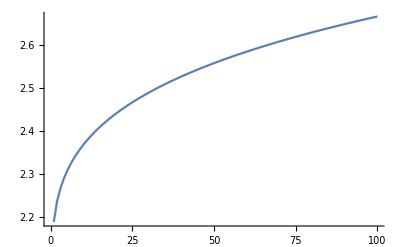

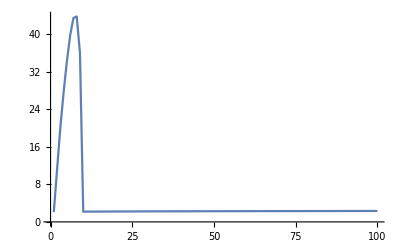

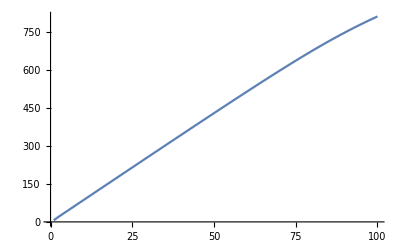

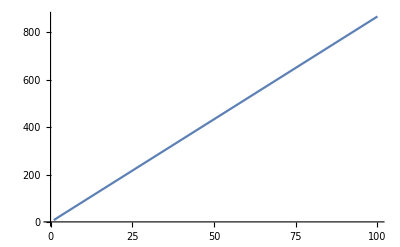

```mathematica
ListLinePlot[InvFitAcrossW270]
ListLinePlot[InvFitAcrossW280,PlotRange->All]
ListLinePlot[InvFitAcrossW290]
ListLinePlot[InvFitAcrossW300]
```

```mathematica
InvFitAcrossW275=Table[CalcInvFit[W,275,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW285=Table[CalcInvFit[W,285,0.9,0.9,1],{W,10,1000,10}];
```

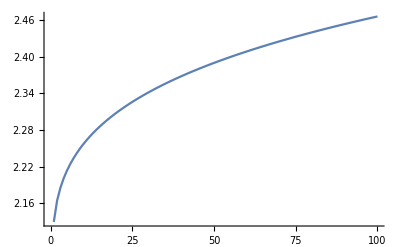

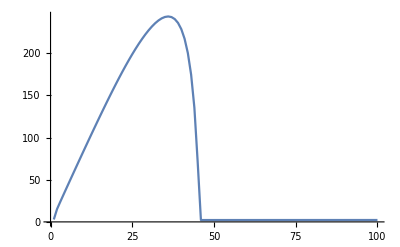

```mathematica
ListLinePlot[InvFitAcrossW275,PlotRange->All]
ListLinePlot[InvFitAcrossW285,PlotRange->All]
```

```mathematica
InvFitAcrossW285
```

{2.86521,15.2938,24.0143,32.5663,41.0645,49.5312,57.9716,66.3859,74.7721,83.1269,91.4458,99.7236,107.954,116.129,124.24,132.277,140.228,148.079,155.815,163.417,170.868,178.146,185.228,192.091,198.709,205.055,211.099,216.807,222.141,227.056,231.497,235.395,238.666,241.2,242.855,243.445,242.717,240.327,235.786,228.384,217.046,200.068,174.574,135.307,71.5263,2.19194,2.19301,2.19407,2.19512,2.19614,2.19715,2.19815,2.19913,2.2001,2.20106,2.202,2.20293,2.20384,2.20475,2.20564,2.20653,2.2074,2.20826,2.20911,2.20995,2.21079,2.21161,2.21242,2.21323,2.21402,2.21481,2.21559,2.21636,2.21713,2.21788,2.21863,2.21937,2.2201,2.22083,2.22155,2.22226,2.22297,2.22367,2.22436,2.22505,2.22573,2.22641,2.22708,2.22774,2.2284,2.22906,2.2297,2.23035,2.23098,2.23162,2.23224,2.23287,2.23349,2.2341,2.23471}

```mathematica
Equilibria=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};D1irValue=Re[D1irEq⟦4,1,2⟧/.allom/.pars];D1sValue=D1sEq⟦1,2⟧/.D1ir->D1irValue/.allom/.pars;NirValue=NirEq⟦1,2⟧/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;NsValue=NsEq⟦1,2⟧/.Nir->NirValue/.allom/.pars;PrValue=PrEq⟦1,2⟧/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars;{NsValue,NirValue,D1sValue,D1irValue,PrValue}];
```

```mathematica
Equilibria[400,285,0.9,0.9,1]
Equilibria[450,285,0.9,0.9,1]
Equilibria[500,285,0.9,0.9,1]
```

{0.183413,0.816587,0.00220181,0.000408801,0.026211}

{0.0223689,0.977631,0.00189653,0.000434161,0.232959}

{0.000509607,0.99949,0.0017321,0.000416207,9.64955}

The problem is that there are multiple equilibria, and I don’t know which one is the correct one to use. That may explain a lot of the goofiness in the response to temperature, if the stable equilibrium switches

```mathematica
D1irEquilibrium=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};D1irEq/.allom/.pars];
D1irEquilibrium[400,285,0.9,0.9,1]
```

{{D1ir→0},{D1ir→0.000469279+3.79471×10^-19 ⅈ},{D1ir→-0.0000540352+2.71051×10^-20 ⅈ},{D1ir→0.000408801-4.06576×10^-19 ⅈ}}

You can see from the numerical simulation that a different equilibrium is stable than what we were looking at in the analytical calculation.

```mathematica
W=400;T=285;f=0.9;NTot=1;
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};NumSol=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==0.1,
Nir[0]==0.9,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==10}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
D1ir[1000]/.NumSol
```

{0.000469279}

```mathematica
NumSolInvFit=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==1,
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
(β Ns NT)/(β Ns NT+γ) ((a1 D1s)/(a1 (D1s+D1ir)+a2 D2s) (c λ1)/μ1+(a2 D2s)/(a1 (D1s+D1ir)+a2 D2s) (c λ2)/μ2)/.{Ns->(Ns[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

```mathematica
NumSolInvFit[400,285,0.9,0.9,1]
```

2.1852

```mathematica
CalcInvFit[400,270,0.9,0.9,1]
NumSolInvFit[400,270,0.9,0.9,1]
```

2.52744

2.52757

Here you can see the very large difference between the two calculations.

```mathematica
CalcInvFit[400,285,0.9,0.9,1]
NumSolInvFit[400,285,0.9,0.9,1]
```

228.384

2.1852

So, I need to recheck to see how the results change:

Now temperature only decreases the invasion fitness, just like with direct life cycle parasites.

```mathematica
Table[NumSolInvFit[400,T,0.9,0.9,1],{T,270,310,5}]
```

{2.52757,2.36788,2.2596,2.1852,2.13343,2.09694,2.07093,2.05218,2.03851}

```mathematica
InvFitAcrossW270=Table[NumSolInvFit[W,270,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW280=Table[NumSolInvFit[W,280,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW290=Table[NumSolInvFit[W,290,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW300=Table[NumSolInvFit[W,300,0.9,0.9,1],{W,10,1000,10}];
InvFitAcrossW310=Table[NumSolInvFit[W,310,0.9,0.9,1],{W,10,1000,10}];
```

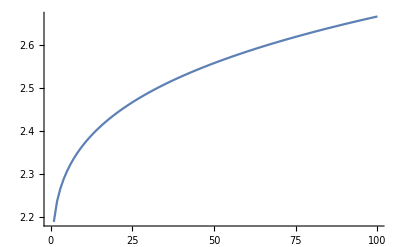

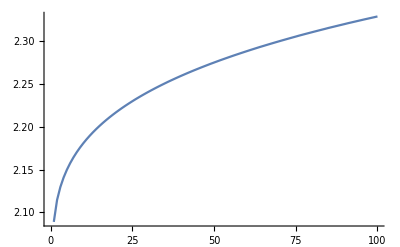

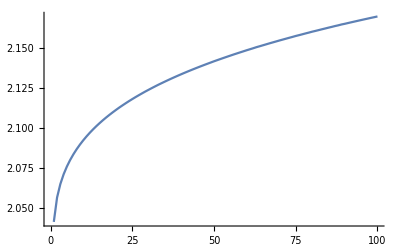

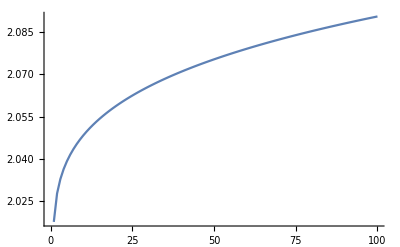

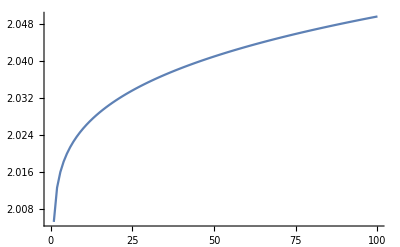

```mathematica
ListLinePlot[InvFitAcrossW270]
ListLinePlot[InvFitAcrossW280,PlotRange->All]
ListLinePlot[InvFitAcrossW290]
ListLinePlot[InvFitAcrossW300]
ListLinePlot[InvFitAcrossW310]
```

```mathematica
D1irEquilibrium=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};D1irEq/.allom/.pars];
```

```mathematica
CalcEquilibria=Function[{W,T,c,f,NTot,D1irValue},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1sValue=D1sEq[[1,2]]/.D1ir->D1irValue/.allom/.pars;
NirValue=NirEq[[1,2]]/.{D1s->D1sValue,D1ir->D1irValue}/.allom/.pars;
{NsEq[[1,2]]/.Nir->NirValue/.allom/.pars,
NirValue,
D1sValue,
PrEq[[1,2]]/.{D1ir->D1irValue,D1s->D1sValue,Nir->NirValue}/.allom/.pars}
];
```

```mathematica
CalcStability=Function[{W,T,c,f,NTot,i},
allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),
μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};
pars={Ε->0.45,k->8.617 10^-5,K0->2.984 10^-9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};
D1irValue=D1irEq[[i,1,2]]/.allom/.pars;
Eqs=CalcEquilibria[W,T,c,f,NTot,D1irValue];
Eigenvalues[Jres/.{D1ir->D1irValue,D1s->Eqs[[3]],Nir->Eqs[[2]],Ns->Eqs[[1]],Pr->Eqs[[4]]}/.allom/.pars]
];
```

```mathematica
NumSolEquilibria=Function[{W,T,c,f,NTot},allom={K1->K0 Exp[Ε/(k T)] W^(-3/4),K2->K0 Exp[Ε/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-Ε/(k T)] W^(-1/4),μ2->μ0 Exp[-Ε/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-Ε/(k T)] W^(3/4),λ2->λ0 Exp[-Ε/(k T)] (f W)^(3/4)};pars={Ε->0.45,k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,β->0.1,γ->0.01,a1->0.1,a2->0.1,r1->0.5,NT->NTot};DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];Soln=NDSolve[({Ns'[t]==a1 (D1s[t]+D1ir[t])+a2 K2-β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t])Ns[t]-a2 K2 Ns[t],
Nir'[t]==β Ns[t] Pr[t]-a1 (D1s[t]+D1ir[t]) Nir[t]-a2 K2 Nir[t],
D1s'[t]==r1 (D1s[t]+D1ir[t]) (1-(D1s[t]+D1ir[t])/K1)-a1 D1s[t] Nir[t] NT,
D1ir'[t]==a1 D1s[t] Nir[t] NT-μ1 D1ir[t],
Pr'[t]==λ1 D1ir[t]-β Ns[t] NT Pr[t]-γ Pr[t],
Ns[0]==1,
Nir[0]==0,
D1s[0]==0.1,
D1ir[0]==0,
Pr[0]==1}/.allom/.pars),
{Ns,Nir,D1s,D1ir,Pr},{t,0,1000},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
{Ns->(Ns[1000]/.Soln)[[1]],Nir->(Nir[1000]/.Soln)[[1]],D1s->(D1s[1000]/.Soln)[[1]],D1ir->(D1ir[1000]/.Soln)[[1]],Pr->(Pr[1000]/.Soln)[[1]]}/.D2s->K2/.allom/.pars
];
```

Here we can confirm that everything agrees with everything else: for these parameters, you find that the second D_(1,I,r) equilibrium is stable and the fourth is unstable, and that the numerical solution goes to the second equilibrium.

```mathematica
(* Numerical calculation of equilibria *)
NumSolEquilibria[400,285,0.9,0.9,1]
(* Analytical calculation of D1ir equilibrium *)
D1irEquilibrium[400,285,0.9,0.9,1]
(* Analytical calculation of second equilibrium *)CalcEquilibria[400,285,0.9,0.9,1,D1irEquilibrium[400,285,0.9,0.9,1][[2,1,2]]]
(* Stability of the second equilibrium *)
CalcStability[400,285,0.9,0.9,1,2]
(* Analytical calculation of fourth equilibrium *)
CalcEquilibria[400,285,0.9,0.9,1,D1irEquilibrium[400,285,0.9,0.9,1][[4,1,2]]]
(* Stability of the fourth equilibrium *)
CalcStability[400,285,0.9,0.9,1,4]
```

{Ns→0.000631818,Nir→0.999368,D1s→0.00206527,D1ir→0.000469279,Pr→9.19172}

{{D1ir→0},{D1ir→0.000469279+3.79471×10^-19 ⅈ},{D1ir→-0.0000540352+2.71051×10^-20 ⅈ},{D1ir→0.000408801-4.06576×10^-19 ⅈ}}

{0.000631785-1.23129×10^-15 ⅈ,0.999368+1.23129×10^-15 ⅈ,0.00206527-8.74519×10^-19 ⅈ,9.19219+1.79252×10^-11 ⅈ}

{-0.919824-1.79268×10^-12 ⅈ,-0.438465+0.183501 ⅈ,-0.438465-0.183501 ⅈ,-0.00999509-1.926×10^-17 ⅈ,-0.000581116+4.95048×10^-20 ⅈ}

{0.183413+1.146×10^-15 ⅈ,0.816587-1.146×10^-15 ⅈ,0.00220181+9.002×10^-19 ⅈ,0.026211-1.98358×10^-16 ⅈ}

{-0.441139-0.17397 ⅈ,-0.441139+0.17397 ⅈ,-0.0553977-1.96213×10^-16 ⅈ,0.0223926+8.84837×10^-17 ⅈ,-0.000588722-4.93624×10^-20 ⅈ}

Whereas for these parameters, you find that the fourth D_(1,I,r) equilibrium is stable and the second is unstable, and that the numerical solution goes to the fourth equilibrium.

```mathematica
(* Numerical calculation of equilibria *)
NumSolEquilibria[400,270,0.9,0.9,1]
(* Analytical calculation of D1ir equilibrium *)
D1irEquilibrium[400,270,0.9,0.9,1]
(* Analytical calculation of second equilibrium *)CalcEquilibria[400,270,0.9,0.9,1,D1irEquilibrium[400,270,0.9,0.9,1][[2,1,2]]]
(* Stability of the second equilibrium *)
CalcStability[400,270,0.9,0.9,1,2]
(* Analytical calculation of fourth equilibrium *)
CalcEquilibria[400,270,0.9,0.9,1,D1irEquilibrium[400,270,0.9,0.9,1][[4,1,2]]]
(* Stability of the fourth equilibrium *)
CalcStability[400,270,0.9,0.9,1,4]
```

{Ns→0.0008184,Nir→0.999182,D1s→0.00451343,D1ir→0.00283781,Pr→20.0466}

{{D1ir→0},{D1ir→0.00569843+3.03577×10^-18 ⅈ},{D1ir→-0.000030503+2.81893×10^-18 ⅈ},{D1ir→0.00283781-5.85469×10^-18 ⅈ}}

{-273.334-4.71654×10^-11 ⅈ,274.334+4.71654×10^-11 ⅈ,0.0000330099-5.65771×10^-18 ⅈ,-0.0148539+1.19746×10^-17 ⅈ}

{-27.4323-4.71672×10^-12 ⅈ,27.3249+4.71654×10^-12 ⅈ,-0.343991+5.01589×10^-16 ⅈ,-0.00147998+2.62194×10^-19 ⅈ,-0.00147434-1.48769×10^-18 ⅈ}

{0.000818357+3.90343×10^-15 ⅈ,0.999182-3.90343×10^-15 ⅈ,0.00451343+8.3206×10^-18 ⅈ,20.0476-9.56992×10^-11 ⅈ}

{-2.00648+9.56962×10^-12 ⅈ,-0.318074-0.111201 ⅈ,-0.318074+0.111201 ⅈ,-0.00999514+4.64646×10^-17 ⅈ,-0.00164196-2.46591×10^-19 ⅈ}

#### True predator-prey model

```mathematica
dNsdt=rN (Ns+Nir) (1-(Ns+Nir)/KN)-β Ns Pr-a1 (D1s+D1ir) Ns;
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=b a1 (D1s+D1ir) (Ns+Nir)-a1 D1s Nir-μ1 D1s;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

Before going any further, notice that the dynamics of the total predator population depend only on the total predator population and the total prey population. Thus we can solve directly for the total prey population at equilibrium.

```mathematica
Simplify[dD1sdt+dD1irdt]
Solve[((dD1sdt+dD1irdt)/.Ns->Ntot-Nir)==0,Ntot]
```

(D1ir+D1s) (a1 b (Nir+Ns)-μ1)

{{Ntot→μ1/(a1 b)}}

From this, you can see that the equilibrium total prey population will be N_S+N_(I,r)=μ_1/(b a_1). At the same time, the dynamics of the total prey population depend only on the total predator and prey populations, so we can also find for the total predator population at equililbrium.

```mathematica
Simplify[dNsdt+dNirdt]
Solve[(dNsdt+dNirdt/.D1s->Dtot-D1ir/.Ns->μ1/(b a1)-Nir)==0,Dtot]
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

This greatly simplifies the dynamics, as we can drop two equations from the systemN_S completely (it is determined entirely by the equilibrium for N_(I,r)) and we can replace N_S+N_(I,r) with μ_1/(b a_1) everywhere else.

Notice that this really simplifies the dynamics of D_(1,S) in particular, from (dD_(1,S))/dt=b a_1(D_(1,S)+D_(1I,r))(N_S+N_(I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1(D_(1,S)+D_(1I,r))-a_1 D_(1,S)N_(I,r)-μ_1 D_(1,S)=μ_1 D_(1I,r)-a_1 D_(1,S)N_(I,r)

```mathematica
dNirdt=dNirdt/.{Ns->μ1/(a1 b)-Nir}/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dD1irdt=dD1irdt/.{D1s->(rN (a1 b KN-μ1))/(a1^2 b KN)-D1ir}
dPrdt=λ1 D1ir-β Ns Pr-γ Pr/.{Ns->μ1/(a1 b)-Nir}
```

-(Nir rN (a1 b KN-μ1))/(a1 b KN)+Pr β (-Nir+μ1/(a1 b))

a1 Nir (-D1ir+(rN (a1 b KN-μ1))/(a1^2 b KN))-D1ir μ1

-Pr γ+D1ir λ1-Pr β (-Nir+μ1/(a1 b))

```mathematica
Simplify[Solve[{dNirdt==0,dD1irdt==0,dPrdt==0},{Nir,D1ir,Pr}]]
```

{{Nir→0,D1ir→0,Pr→0},{Nir→(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))/(2 a1^2 b β),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1-a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))},{Nir→(a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))/(2 a1^2 b β),D1ir→1/(4 a1^4 b^2 (1+b) KN β^2 λ1 μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1+a1 b β μ1-√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))),Pr→-1/(4 a1^4 b^2 (1+b) KN β^2 γ μ1)rN (a1 b KN-μ1) (a1^2 b γ+a1 b β λ1+a1 β μ1-a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2))) (-a1^2 b γ-a1 b β λ1+a1 β μ1+a1 b β μ1+√(a1^2 (4 b β μ1 (a1 b γ+β (-λ1+μ1))+(a1 b γ+β (b (λ1-μ1)+μ1))^2)))}}

```mathematica
dNirdt=β Ns Pr-a1 (D1s+D1ir) Nir ;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

-((Nir+Ns) (a1 (D1ir+D1s) KN+(-KN+Nir+Ns) rN))/KN

{{Dtot→(rN (a1 b KN-μ1))/(a1^2 b KN)}}

```mathematica
dNirdt=β (μ1/(b a1)-Nir) Pr-a1 (D1s+D1ir) Nir ;
dD1sdt=μ1 D1ir-a1 D1s Nir;
dD1irdt=a1 D1s Nir-μ1 D1ir;
dPrdt=λ1 D1ir-β Ns Pr-γ Pr;
```

```mathematica
D1sEq=Simplify[Solve[dNirdt==0,D1s]]
```

{{D1s→-D1ir+(Pr β (-a1 b Nir+μ1))/(a1^2 b Nir)}}

```mathematica
D1irEq=Solve[dPrdt==0,D1ir][[1]]
```

{D1ir→(Ns Pr β+Pr γ)/λ1}

```mathematica
NirEq=Solve[(dD1irdt/.D1irEq)==0,Nir][[1]]
```

{Nir→((Ns Pr β+Pr γ) μ1)/(a1 D1s λ1)}

```mathematica
D1sEq=Solve[(dD1sdt/.NirEq/.D1irEq)==0,D1s][[2]]
```

{D1s→-(-b Ns Pr β μ1-b Pr γ μ1)/(λ1 (-a1 b Ns+μ1))}

```mathematica
NsEq=Solve[Simplify[dNirdt/.D1irEq/.NirEq/.D1sEq]==0,Ns][[2]]
```

{Ns→(-a1 b γ-b β λ1+β μ1+b β μ1+√((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(2 a1 b β)}

```mathematica
Solve[Numerator[Together[dNsdt/.D1irEq/.NirEq/.D1sEq/.NsEq]]==0,Pr][[1]]
```

{Pr→(-a1^2 b^2 KN rN γ μ1-a1 b^2 KN rN β λ1 μ1-a1 b KN rN β μ1^2+a1 b^2 KN rN β μ1^2+a1 b rN γ μ1^2+b rN β λ1 μ1^2+rN β μ1^3-b rN β μ1^3+a1 b KN rN μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1))-rN μ1^2 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))/(a1^2 b^2 KN β γ μ1+a1 b^2 KN β^2 λ1 μ1-a1 b KN β^2 μ1^2-a1 b^2 KN β^2 μ1^2-a1 b KN β μ1 √((a1 b γ+b β λ1-β μ1-b β μ1)^2-4 a1 b β (-γ μ1-b γ μ1)))}

```mathematica
K
```

K

```mathematica
dX=r X (1-X/K)-a X Y;
dY=b X Y-m Y;
```

```mathematica
Solve[dY==0,X]
Solve[dX==0,Y]/.{X->m/b}//Simplify
```

{{X→m/b}}

{{Y→((K-m/b) r)/(a K)}}

$Aborted

#### A model with two intermediate hosts, each eaten by a single definitive host: when can a generalist that infects both intermediate hosts and both definitive hosts invade?

This model has the advantage of being a bit more analytically tractable. We assume that there are two intermediate hosts, N_1 and N_2. As before, both of these have constant population sizes of N_(1T) and N_(2T), so we need only keep track of the abundance of infected intermediate hosts. We let N_(1I r) and N_(2I r) be the number of intermediate hosts infected by the resident specialist parasites and N_(1I m) and N_(2I m) be the number of intermediate hosts infected by the mutant generalist parasite. We assume that these intermediate hosts are eaten by predator that serves as the definitive host for the parasites. Each intermediate host has its own definitive host. We let D_(1S) and D_(2S) be the numbers of definitive hosts that are susceptible to infection, D_(1I r) and D_(2 I r) be the numbers of definitive hosts infected by the resident specialist parasites, and D_(1I m) and D_(2 I m) be the numbers of infected by the mutant generalist parasite. Parasites are shed from the definitive hosts back into the environment, and we let P_(1r), P_(2r), and P_m track the abundance of the two specialists and the generalist parasite.

We assume that the parasite actively seeks out susceptible intermediate hosts. Intermediate hosts, however, are eaten by both susceptible and infected definitive hosts. However, we assume that definitive host 1 only eats intermediate host 1, and definitive host 2 only eats intermediate host 2.

```mathematica
dN1irdt=β (N1T-N1ir-N1im) P1r-a1(D1s+D1ir+D1im) N1ir;
dN2irdt=β (N2T-N2ir-N2im) P2r-a2(D2s+D2ir+D2im) N2ir;
dN1imdt=β (N1T-N1ir-N1im) Pm-a1(D1s+D1ir+D1im) N1im;
dN2imdt=β (N2T-N2ir-N2im) Pm-a2(D2s+D2ir+D2im) N2im;

dD1sdt=r1 (D1s+D1ir+D1im)(1-(D1s+D1ir+D1im)/K1)-a1 D1s (N1ir+N1im);
dD2sdt=r2 (D2s+D2ir+D2im)(1-(D2s+D2ir+D2im)/K2)-a2 D2s (N2ir+N2im);
dD1irdt=a1 D1s N1ir-μ1 D1ir;
dD2irdt=a2 D2s N2ir-μ2 D2ir;
dD1imdt=a1 D1s N1im-μ1 D1im;
dD2imdt=a2 D2s N2im-μ2 D2im;

dP1rdt=λ1 D1ir-β (N1T-N1ir-N1im) P1r-γ P1r;
dP2rdt=λ2 D2ir-β (N2T-N2ir-N2im) P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β (N1T-N1ir-N1im+N2T-N2ir-N2im) Pm-γ Pm;
```

For persistence of the first definitive host, we require only that r_1>0:

```mathematica
{{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r]}}/.{D1s->0,D1ir->0,D1im->0,P1r->0,N1ir->0,N1im->0}//Eigenvalues
```

{0,r1,-N1T β-γ,-μ1}

For persistence of the first specialist parasite, we require that (β N_(1T))/(β N_(1T)+γ)λ_1/μ_1>1, which is just the probability that a specialist parasite in the environment ends up in an intermediate host multiplied by the expected number of new parasites produced by an infected definitive host (because all intermediate hosts are assumed to end up eaten by definitive hosts).

```mathematica
{{D[dN1irdt,N1ir],D[dN1irdt,D1s],D[dN1irdt,D1ir],D[dN1irdt,P1r]},
{D[dD1sdt,N1ir],D[dD1sdt,D1s],D[dD1sdt,D1ir],D[dD1sdt,P1r]},
{D[dD1irdt,N1ir],D[dD1irdt,D1s],D[dD1irdt,D1ir],D[dD1irdt,P1r]},
{D[dP1rdt,N1ir],D[dP1rdt,D1s],D[dP1rdt,D1ir],D[dP1rdt,P1r]}}/.{D1s->K1,D1ir->0,D1im->0,P1r->0,N1ir->0,N1im->0}//MatrixForm
F={{0,0,0,N1T β},{0,0,0,0},{a1 K1,0,0,0},{0,0,λ1,0}};
V={{a1 K1,0,0,0},{a1 K1,r1,r1,0},{0,0,μ1,0},{0,0,0,N1T β+γ}};
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]])^3
```

(-a1 K1 | 0 | 0 | N1T β
-a1 K1 | -r1 | -r1 | 0
a1 K1 | 0 | -μ1 | 0
0 | 0 | λ1 | -N1T β-γ)

{0,(N1T^(1/3) β^(1/3) λ1^(1/3))/((N1T β+γ)^(1/3) μ1^(1/3)),-((-1)^(1/3) N1T^(1/3) β^(1/3) λ1^(1/3))/((N1T β+γ)^(1/3) μ1^(1/3)),((-1)^(2/3) N1T^(1/3) β^(1/3) λ1^(1/3))/((N1T β+γ)^(1/3) μ1^(1/3))}

{0,(N1T β λ1)/((N1T β+γ) μ1),(N1T β λ1)/((N1T β+γ) μ1),(N1T β λ1)/((N1T β+γ) μ1)}

For persistence of the second specialist parasite, we require that (β N_(2T))/(β N_(2T)+γ)λ_2/μ_2>1, which is just the probability that a specialist parasite in the environment ends up in an intermediate host multiplied by the expected number of new parasites produced by an infected definitive host (because all intermediate hosts are assumed to end up eaten by definitive hosts).

```mathematica
{{D[dN2irdt,N2ir],D[dN2irdt,D2s],D[dN2irdt,D2ir],D[dN2irdt,P2r]},
{D[dD2sdt,N2ir],D[dD2sdt,D2s],D[dD2sdt,D2ir],D[dD2sdt,P2r]},
{D[dD2irdt,N2ir],D[dD2irdt,D2s],D[dD2irdt,D2ir],D[dD2irdt,P2r]},
{D[dP2rdt,N2ir],D[dP2rdt,D2s],D[dP2rdt,D2ir],D[dP2rdt,P2r]}}/.{D2s->K2,D2ir->0,D2im->0,P2r->0,N2ir->0,N2im->0}//MatrixForm
F={{0,0,0,N2T β},{0,0,0,0},{a2 K2,0,0,0},{0,0,λ2,0}};
V={{a2 K2,0,0,0},{a2 K2,r2,r2,0},{0,0,μ2,0},{0,0,0,N2T β+γ}};
Eigenvalues[Dot[F,Inverse[V]]]
(Eigenvalues[Dot[F,Inverse[V]]])^3
```

(-a2 K2 | 0 | 0 | N2T β
-a2 K2 | -r2 | -r2 | 0
a2 K2 | 0 | -μ2 | 0
0 | 0 | λ2 | -N2T β-γ)

{0,(N2T^(1/3) β^(1/3) λ2^(1/3))/((N2T β+γ)^(1/3) μ2^(1/3)),-((-1)^(1/3) N2T^(1/3) β^(1/3) λ2^(1/3))/((N2T β+γ)^(1/3) μ2^(1/3)),((-1)^(2/3) N2T^(1/3) β^(1/3) λ2^(1/3))/((N2T β+γ)^(1/3) μ2^(1/3))}

{0,(N2T β λ2)/((N2T β+γ) μ2),(N2T β λ2)/((N2T β+γ) μ2),(N2T β λ2)/((N2T β+γ) μ2)}

We can also attempt to directly solve for the equilibria.

```mathematica
D1sEq=Simplify[Solve[dN1irdt==0,D1s]/.{D1im->0,N1im->0}]
```

{{D1s→(-a1 D1ir N1ir+(-N1ir+N1T) P1r β)/(a1 N1ir)}}

```mathematica
D1irEq=Simplify[Solve[(dD1sdt/.D1sEq[[1]]/.{D1im->0,N1im->0})==0,D1ir]]
```

{{D1ir→-((N1ir-N1T) P1r β (a1^2 K1 N1ir^2-a1 K1 N1ir r1+(-N1ir+N1T) P1r r1 β))/(a1^3 K1 N1ir^3)}}

```mathematica
P1rEq=Solve[(dD1irdt/.D1sEq[[1]]/.D1irEq[[1]])==0,P1r]
```

{{P1r→0},{P1r→-(a1 K1 N1ir (a1 N1ir r1-a1 N1ir μ1+r1 μ1))/((N1ir-N1T) r1 β (a1 N1ir+μ1))}}

```mathematica
N1irEq=Solve[(dP1rdt/.D1irEq[[1]]/.P1rEq[[2]]/.N1im->0)==0,N1ir]
```

{{N1ir→0},{N1ir→-(r1 μ1)/(a1 (r1-μ1))},{N1ir→(a1 N1T β+a1 γ+β λ1-β μ1-√((-a1 N1T β-a1 γ-β λ1+β μ1)^2-4 a1 β (N1T β λ1-N1T β μ1-γ μ1)))/(2 a1 β)},{N1ir→(a1 N1T β+a1 γ+β λ1-β μ1+√((-a1 N1T β-a1 γ-β λ1+β μ1)^2-4 a1 β (N1T β λ1-N1T β μ1-γ μ1)))/(2 a1 β)}}

The square root term can be rewritten slightly as (β (λ1-μ1)-a1 (β N1T+γ))^2+4 a1 β γ λ1, which is clearly positive, meaning that it is impossible to ever get an imaginary equilibrium point.

```mathematica
Expand[(-a1 N1T β-a1 γ-β λ1+β μ1)^2-4 a1 β (N1T β λ1-N1T β μ1-γ μ1)]==(β (λ1-μ1)-a1 (β N1T+γ))^2+4 a1 β γ λ1//Simplify
```

True

We can determine for what parameter values the third, rather than the fourth, N_(1I r) equilibrium will be positive. Since we know that the expression under the square root sign is always positive, we can square both sides of the inequality

```mathematica
a1 N1T β+a1 γ+β λ1-β μ1>√((-a1 N1T β-a1 γ-β λ1+β μ1)^2-4 a1 β (N1T β λ1-N1T β μ1-γ μ1));
Simplify[Expand[(a1 N1T β+a1 γ+β λ1-β μ1)^2>(-a1 N1T β-a1 γ-β λ1+β μ1)^2-4 a1 β (N1T β λ1-N1T β μ1-γ μ1)]]
```

a1 β (N1T β (λ1-μ1)-γ μ1)>0

Notice, however, that the criterion for the specialist parasite to be able to persist is (β N_(1T))/(β N_(1T)+γ)λ_1/μ_1>1, which can be rewritten as β N_(1T)(λ_1-μ_1)-γ μ_1>0, meaning that the third equilibrium is always positive and real.

```mathematica
pars={β->1,N1T->1,λ1->5,γ->1,μ1->1,a1->1,K1->0.1,r1->0.6};
Soln=NDSolve[{N1ir'[t]==(dN1irdt/.{D1im->0,N1im->0,D1ir->D1ir[t],D1s->D1s[t],N1ir->N1ir[t],P1r->P1r[t]}),
D1s'[t]==(dD1sdt/.{D1im->0,N1im->0,D1ir->D1ir[t],D1s->D1s[t],N1ir->N1ir[t],P1r->P1r[t]}),
D1ir'[t]==(dD1irdt/.{D1im->0,N1im->0,D1ir->D1ir[t],D1s->D1s[t],N1ir->N1ir[t],P1r->P1r[t]}),
P1r'[t]==(dP1rdt/.{D1im->0,N1im->0,D1ir->D1ir[t],D1s->D1s[t],N1ir->N1ir[t],P1r->P1r[t]}),
N1ir[0]==0,D1s[0]==K1,D1ir[0]==0,P1r[0]==1}/.pars,{N1ir,D1s,D1ir,P1r},{t,0,10000}];
{N[N1irEq[[3]]/.pars],P1rEq[[2]]/.N1irEq[[3]]/.pars,D1irEq/.P1rEq[[2]]/.N1irEq[[3]]/.pars,D1sEq/.D1irEq/.P1rEq[[2]]/.N1irEq[[3]]/.pars}
{N1ir[10000],P1r[10000],D1ir[10000],D1s[10000]}/.Soln
```

{{N1ir→0.55051},{P1r→0.05},{{D1ir→0.0144949}},{{{D1s→0.0263299}}}}

{{0.55051,0.05,0.0144949,0.0263299}}

#### constant predator population size

```mathematica
dN1rdt=β (KN-N1r-N2r-N12m) P1r-c N1r (K1+K2);
dN2rdt=β (KN-N1r-N2r-N12m) P2r-c N2r (K1+K2);
dN12mdt=β (KN-N1r-N2r-N12m) P12m-c N12m (K1+K2);

dI1rdt=c(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=c(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=c(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=c(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r KN-γ P1r;
dP2rdt=λ2 I2r-β P2r KN-γ P2r;
dP12mdt=a λ1 I1m+a λ2 I2m-β P12m KN-γ P12m;
```

```mathematica
dN1irdt=β (N1T-N1ir-N1im) P1r-a1 D1T N1ir;
dN2irdt=β (N2T-N2ir-N2im) P2r-a2 D2T N2ir;
dN1imdt=β (N1T-N1ir-N1im) Pm-a1 D1T N1im;
dN2imdt=β (N2T-N2ir-N2im) Pm-a2 D2T N2im;

dD1irdt=a1 (D1T-D1ir-D1im) N1ir-μ1 D1ir;
dD2irdt=a2 (D2T-D2ir-D2im) N2ir-μ2 D2ir;
dD1imdt=a1 (D1T-D1ir-D1im) N1im-μ1 D1im;
dD2imdt=a2 (D2T-D2ir-D2im) N2im-μ2 D2im;

dP1rdt=λ1 D1ir-β (N1T-N1ir-N1im) P1r-γ P1r;
dP2rdt=λ2 D2ir-β (N2T-N2ir-N2im) P2r-γ P2r;
dPmdt=c λ1 D1im+c λ2 D2im-β (N1T-N1ir-N1im+N2T-N2ir-N2im) Pm-γ Pm;
```

```mathematica
Solve[dN1irdt==0,P1r]
```

{{P1r→-(a1 D1T N1ir)/((N1im+N1ir-N1T) β)}}

```mathematica
Solve[dD1irdt==0,N1ir]
```

{{N1ir→-(D1ir μ1)/(a1 (D1im+D1ir-D1T))}}

```mathematica
D1irEq=Solve[(dP1rdt/.{P1r->-(a1 D1T N1ir)/((N1im+N1ir-N1T) β)}/.{N1ir->-(D1ir μ1)/(a1 (D1im+D1ir-D1T))}/.D1im->0/.N1im->0)==0,D1ir]
```

{{D1ir→0},{D1ir→1/(2 (a1 N1T β λ1+β λ1 μ1))(2 a1 D1T N1T β λ1-a1 D1T N1T β μ1-a1 D1T γ μ1+D1T β λ1 μ1-D1T β μ1^2-√(-4 (a1 D1T^2 N1T β λ1-a1 D1T^2 N1T β μ1-a1 D1T^2 γ μ1) (a1 N1T β λ1+β λ1 μ1)+(-2 a1 D1T N1T β λ1+a1 D1T N1T β μ1+a1 D1T γ μ1-D1T β λ1 μ1+D1T β μ1^2)^2))},{D1ir→1/(2 (a1 N1T β λ1+β λ1 μ1))(2 a1 D1T N1T β λ1-a1 D1T N1T β μ1-a1 D1T γ μ1+D1T β λ1 μ1-D1T β μ1^2+√(-4 (a1 D1T^2 N1T β λ1-a1 D1T^2 N1T β μ1-a1 D1T^2 γ μ1) (a1 N1T β λ1+β λ1 μ1)+(-2 a1 D1T N1T β λ1+a1 D1T N1T β μ1+a1 D1T γ μ1-D1T β λ1 μ1+D1T β μ1^2)^2))}}

```mathematica
Simplify[Solve[dD1irdt==0,N1ir]/.D1irEq[[2]]/.D1im->0]
```

{{N1ir→-(μ1 (-D1T β λ1 μ1+D1T β μ1^2+a1 D1T (γ μ1+N1T β (-2 λ1+μ1))+√(D1T^2 μ1^2 (a1^2 (N1T β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (N1T β (-λ1+μ1)+γ (λ1+μ1))))))/(a1 (a1 D1T N1T β μ1+a1 D1T γ μ1+D1T β λ1 μ1+D1T β μ1^2+√(D1T^2 μ1^2 (a1^2 (N1T β+γ)^2+β^2 (λ1-μ1)^2+2 a1 β (N1T β (-λ1+μ1)+γ (λ1+μ1))))))}}

```mathematica
D1sEq=Solve[dD1irdt==0,D1s]
```

{{D1s→(D1ir μ1)/(a1 N1ir)}}

```mathematica
Solve[FullSimplify[dD1sdt/.D1sEq[[1]]/.D1im->0/.N1im->0]==0,N1ir]
```

{{N1ir→(-2 a1 D1ir r1 μ1+a1 K1 r1 μ1-√(a1^2 K1^2 r1^2 μ1^2-4 a1^2 D1ir K1 r1 μ1^3))/(2 (a1^2 D1ir r1-a1^2 K1 r1+a1^2 K1 μ1))},{N1ir→(-2 a1 D1ir r1 μ1+a1 K1 r1 μ1+√(a1^2 K1^2 r1^2 μ1^2-4 a1^2 D1ir K1 r1 μ1^3))/(2 (a1^2 D1ir r1-a1^2 K1 r1+a1^2 K1 μ1))}}

```mathematica
Simplify[D[D1sEq[[1,1,2]]/.{D1ir->D1ir[W],μ1->μ1[W],N1ir->N1ir[W]},W]]
Numerator[Simplify[D[D1sEq[[1,1,2]]/.{D1ir->D1ir[W],μ1->μ1[W],N1ir->N1ir[W]},W]]]
```

(N1ir[W] μ1[W] D1ir'[W]-D1ir[W] μ1[W] N1ir'[W]+D1ir[W] N1ir[W] μ1'[W])/(a1 N1ir[W]^2)

N1ir[W] μ1[W] D1ir'[W]-D1ir[W] μ1[W] N1ir'[W]+D1ir[W] N1ir[W] μ1'[W]

```mathematica
D[dD1sdt/.{D1im->0,N1im->0}/.{D1ir->D1ir[W],μ1->μ1[W],N1ir->N1ir[W],D1s->D1s[W],r1->r1[W],K1->K1[W]},W]
```

-a1 N1ir[W] D1s'[W]+(1-(D1ir[W]+D1s[W])/K1[W]) r1[W] (D1ir'[W]+D1s'[W])+(D1ir[W]+D1s[W]) r1[W] (-(D1ir'[W]+D1s'[W])/K1[W]+((D1ir[W]+D1s[W]) K1'[W])/K1[W]^2)-a1 D1s[W] N1ir'[W]+(D1ir[W]+D1s[W]) (1-(D1ir[W]+D1s[W])/K1[W]) r1'[W]

#### A model with two intermediate hosts and constant host population sizes

```mathematica
dN1rdt=β (KN1-N1r-N12m) P1r-a N1r K1;
dN2rdt=β (KN2-N2r-N12m) P2r-a N2r K2;
dN12mdt=β (KN-N1r-N2r-N12m) P12m-a N12m (K1+K2);

dI1rdt=a(K1-I1r-I1m) N1r-μ1 I1r;
dI2rdt=a(K2-I2r-I2m) N2r-μ2 I2r;
dI1mdt=a(K1-I1r-I1m) N12m-μ1 I1m;
dI2mdt=a(K2-I2r-I2m) N12m-μ2 I2m;

dP1rdt=λ1 I1r-β P1r (KN1-N1r-N12m)-γ P1r;
dP2rdt=λ2 I2r-β P2r (KN2-N2r-N12m)-γ P2r;
dP12mdt=c λ1 I1m+c λ2 I2m-β P12m (KN-N1r-N2r-N12m)-γ P12m;
```

To find the generalist-free equilibrium, we first make use of the fact that (dP_(1r))/dt=0 implies that β P_(1r)(K_N-N_(1r)-N_(2r))=λ_1 I_(1r)-γ P_(1r) and that (dP_(2r))/dt=0 implies that β P_(2r)(K_N-N_(1r)-N_(2r))=λ_2 I_(2r)-γ P_(2r).

```mathematica
I1rEq=Solve[λ1 I1r-γ P1r-a N1r K1==0,I1r][[1,1,2]]
I2rEq=Solve[λ2 I2r-γ P2r-a N2r K2==0,I2r][[1,1,2]]
```

(a K1 N1r+P1r γ)/λ1

(a K2 N2r+P2r γ)/λ2

```mathematica
P1rEq=Solve[(dI1rdt/.{I1r->I1rEq,I1m->0})==0,P1r][[1,1,2]]
P2rEq=Solve[(dI2rdt/.{I2r->I2rEq,I2m->0})==0,P2r][[1,1,2]]
```

(-a^2 K1 N1r^2+a K1 N1r λ1-a K1 N1r μ1)/(γ (a N1r+μ1))

(-a^2 K2 N2r^2+a K2 N2r λ2-a K2 N2r μ2)/(γ (a N2r+μ2))

```mathematica
I1rEq=I1rEq/.P1r->P1rEq//Simplify
I2rEq=I2rEq/.P2r->P2rEq//Simplify
```

(a K1 N1r)/(a N1r+μ1)

(a K2 N2r)/(a N2r+μ2)

```mathematica
N1rEq=Simplify[Solve[Numerator[Simplify[dP1rdt/.I1r->I1rEq/.N12m->0/.P1r->P1rEq]]==0,N1r]]
N2rEq=Simplify[Solve[Numerator[Simplify[dP2rdt/.I2r->I2rEq/.N12m->0/.P2r->P2rEq]]==0,N2r]]
```

{{N1r→0},{N1r→(a KN1 β+a γ+β λ1-β μ1-√((a (KN1 β+γ)+β (λ1-μ1))^2-4 a β (KN1 β (λ1-μ1)-γ μ1)))/(2 a β)},{N1r→(a KN1 β+a γ+β λ1-β μ1+√((a (KN1 β+γ)+β (λ1-μ1))^2-4 a β (KN1 β (λ1-μ1)-γ μ1)))/(2 a β)}}

{{N2r→0},{N2r→(a KN2 β+a γ+β λ2-β μ2-√((a (KN2 β+γ)+β (λ2-μ2))^2-4 a β (KN2 β (λ2-μ2)-γ μ2)))/(2 a β)},{N2r→(a KN2 β+a γ+β λ2-β μ2+√((a (KN2 β+γ)+β (λ2-μ2))^2-4 a β (KN2 β (λ2-μ2)-γ μ2)))/(2 a β)}}

```mathematica
Simplify[K1-I1rEq/.N1rEq[[2]]]
Simplify[K2-I2rEq/.N2rEq[[2]]]
```

(2 K1 β μ1)/(a KN1 β+a γ+β λ1+β μ1-√((a (KN1 β+γ)+β (λ1-μ1))^2-4 a β (KN1 β (λ1-μ1)-γ μ1)))

(2 K2 β μ2)/(a KN2 β+a γ+β λ2+β μ2-√((a (KN2 β+γ)+β (λ2-μ2))^2-4 a β (KN2 β (λ2-μ2)-γ μ2)))

```mathematica
KN1-(a KN1 β+a γ+β λ1-β μ1-√((a (KN1 β+γ)+β (λ1-μ1))^2-4 a β (KN1 β (λ1-μ1)-γ μ1)))/(2 a β)//Simplify
```

(a KN1 β-a γ-β λ1+β μ1+√((a (KN1 β+γ)+β (λ1-μ1))^2-4 a β (KN1 β (λ1-μ1)-γ μ1)))/(2 a β)